# Computation of λ_(E,H) for the diagonal matrix element

```mathematica
SetDirectory["/home/muslem-rahimi/Doktorarbeit/Notes/LiteRed/Setup"];
<<LiteRed`;
SetDirectory["/home/muslem-rahimi/Doktorarbeit/Notes"];
<<RunDec`;
<<FeynCalc`;
```

**************** LiteRed v1.82 ********************
Author: Roman N. Lee, Budker Institute of Nuclear Physics, Novosibirsk.
Release Date: 01.06.2015
LiteRed stands for Loop InTEgrals REDuction.
The package is designed for the search and application of the Integration-By-Part reduction rules. It also contains some other useful tools.
See ?LiteRed`* for a list of functions.

RunDec: a Mathematica package for running and decoupling of the

strong coupling and quark masses

by K.G. Chetyrkin, J.H. K\"uhn and M. Steinhauser (January 2000)

by F. Herren and M. Steinhauser (April 2016, v2.1)

FeynCalc is already loaded! If you are trying to reload FeynCalc or load FeynArts, TARCER, PHI, FeynHelpers or any other add-on, please restart the kernel.

$Aborted

```mathematica
(*Tanaka's Subscript[α, S]*)
AlphasLam[0.31,1,4,2]

LamExpl[asMz/.NumDef,Mz/.NumDef,4,4]
AlphasLam[0.38,1,4,4];
```

0.470854

0.38952

## Tensor reduction

### Master Integral

```mathematica
MasterIntegral[p_,α_,Δ_,β_]:=μ^(2*ϵ)*I*(-1)^(α+β)/(2^(d)*Pi^(d/2))*Gamma[α+d/2]*
Gamma[β-α-d/2]/(Gamma[d/2]*Gamma[β])*Δ^(α-β+d/2)
```

### TwoLoop

```mathematica
FCClearScalarProducts[];
denrule={Den1[vk]^α1_*Den2[l]^α2_*Den3[k+l-v*ω]^α3_*Den4[k]^α4_*Den5[kl]^α5_-> j[MI,α1-1000,α2-1000,α3-1000,-α4+1000,-α5+1000]};
int1=-Tdec[{{el,μ},{el,ρ},{k,x}},{v},List->False]*GAD[x]*MTD[ν,σ]+Tdec[{{el,ν},{el,ρ},{k,x}},{v},List->False]*GAD[x]*MTD[μ,σ]+Tdec[{{el,μ},{el,σ},{k,x}},{v},List->False]*GAD[x]*MTD[ν,ρ]-Tdec[{{el,ν},{el,σ},{k,x}},{v},List->False]*GAD[x]*MTD[μ,ρ];

int2 = ω*Tdec[{{el,μ},{el,ρ},{v,x}},{v},List->False]*GAD[x]*MTD[ν,σ]-ω*Tdec[{{el,ν},{el,ρ},{v,x}},{v},List->False]*GAD[x]*MTD[μ,σ]-ω*Tdec[{{el,μ},{el,σ},{v,x}},{v},List->False]*GAD[x]*MTD[ν,ρ]+ ω*Tdec[{{el,ν},{el,σ},{v,x}},{v},List->False]*GAD[x]*MTD[μ,ρ];
int3=  -Tdec[{{el,μ},{el,ρ},{el,x}},{v},List->False]*GAD[x]*MTD[ν,σ]+Tdec[{{el,ν},{el,ρ},{el,x}},{v},List->False]*GAD[x]*MTD[μ,σ]+Tdec[{{el,μ},{el,σ},{el,x}},{v},List->False]*GAD[x]*MTD[ν,ρ]-Tdec[{{el,ν},{el,σ},{el,x}},{v},List->False]*GAD[x]*MTD[μ,ρ];

int = int1+int2+int3//Contract//Expand;


SPD[v,v]=1;
SPD[el,v]=vl;
SPD[el,el]=l2;
SPD[k,v]=kv;
SPD[k,el]=lk;

final=Den1[vk]*Den2[l]*Den3[l+k-v*ω]*int/.kv->Den1[vk]^(-1)/.l2->Den2[l]^(-1)/.lk->Den5[kl]/.vl->(-1/(2*ω))*(Den3[l+k-v*ω]^(-1)-Den4[k]-Den2[l]^(-1)-ω^2-2*Den5[kl]+2*Den1[vk]^(-1)*ω)//Expand;

final=Expand[Den1[vk]^1000*Den2[l]^1000*Den3[l+k-v*ω]^1000*Den4[k]^1000*Den5[kl]^1000*final]/.D->4/.d->4/.denrule;
```

##### Reduce to MIs

```mathematica
SetDim[d];
Declare[{p,q,k,v,l},Vector,{m,M,ω},Number]
NewBasis[MI,{sp[k,v],sp[l,l],sp[l+k-v*ω,l+k-v*ω],sp[k,k],sp[k,l]},{k,l},Directory->"shell2"]

sp[v,v]=1;
GenerateIBP[MI];
AnalyzeSectors[MI];
FindSymmetries[MI];
SolvejSector/@UniqueSectors[MI];
```

Valid basis.
    Ds[MI] — denominators,
    SPs[MI] — scalar products involving loop momenta,
    LMs[MI] — loop momenta,
    EMs[MI] — external momenta,
    Toj[MI] — rules to transform scalar products to denominators.
The definitions of the basis will be saved in shell2

DiskSave::overwrite: The file shell2/MI has been overwritten.

Integration-By-Part&Lorentz-Invariance identities are generated.
    IBP[MI] — integration-by-part identities,
    LI[MI] — Lorentz invariance identities.

Found 21 zero sectors out of 32.
    ZeroSectors[MI] — zero sectors,
    NonZeroSectors[MI] — nonzero sectors,
    SimpleSectors[MI] — simple sectors (no nonzero subsectors),
    BasisSectors[MI] — basis sectors (at least one immediate subsector is zero),
    ZerojRule[MI] — a rule to nullify all zero j[MI…],
    CutDs[MI] — a flag list of cut denominatorsj (1=cut).

Found 1 mapped sectors and 10 unique sectors.
    UniqueSectors[MI] — unique sectors.
    MappedSectors[MI] — mapped sectors.
    SR[MI][…] — symmetry relations for j[MI,…] from UniqueSectors[MI].
    jSymmetries[MI,…] — symmetry rules for the sector js[MI,…] in UniqueSectors[MI].
    jRules[MI,…] — reduction rules for j[MI,…] from MappedSectors[MI].

Sector js(MI,0,0,1,0,1)

DiskSave::overwrite: The file shell2/jRules[MI, 0, 0, 1, 0, 1] has been overwritten.

1 master integrals found:
j[MI, 0, 0, 1, 0, 1].
    jRules[MI, 0, 0, 1, 0, 1] — reduction rules for the sector.
    MIs[MI] — updated list of the masters.

Sector js(MI,0,0,1,1,1)

DiskSave::overwrite: The file shell2/jRules[MI, 0, 0, 1, 1, 1] has been overwritten.

0 master integrals found.
    jRules[MI, 0, 0, 1, 1, 1] — reduction rules for the sector.
    MIs[MI] — updated list of the masters.

Sector js(MI,0,1,1,1,0)

DiskSave::overwrite: The file shell2/jRules[MI, 0, 1, 1, 1, 0] has been overwritten.

General::stop: Further output of DiskSave::overwrite will be suppressed during this calculation.

1 master integrals found:
j[MI, 0, 1, 1, 1, 0].
    jRules[MI, 0, 1, 1, 1, 0] — reduction rules for the sector.
    MIs[MI] — updated list of the masters.

Sector js(MI,1,0,1,0,1)

0 master integrals found.
    jRules[MI, 1, 0, 1, 0, 1] — reduction rules for the sector.
    MIs[MI] — updated list of the masters.

Sector js(MI,1,1,1,0,0)

1 master integrals found:
j[MI, 1, 1, 1, 0, 0].
    jRules[MI, 1, 1, 1, 0, 0] — reduction rules for the sector.
    MIs[MI] — updated list of the masters.

Sector js(MI,0,1,1,1,1)

0 master integrals found.
    jRules[MI, 0, 1, 1, 1, 1] — reduction rules for the sector.
    MIs[MI] — updated list of the masters.

Sector js(MI,1,0,1,1,1)

0 master integrals found.
    jRules[MI, 1, 0, 1, 1, 1] — reduction rules for the sector.
    MIs[MI] — updated list of the masters.

Sector js(MI,1,1,1,0,1)

1 master integrals found:
j[MI, 1, 1, 1, 0, 1].
    jRules[MI, 1, 1, 1, 0, 1] — reduction rules for the sector.
    MIs[MI] — updated list of the masters.

Sector js(MI,1,1,1,1,0)

0 master integrals found.
    jRules[MI, 1, 1, 1, 1, 0] — reduction rules for the sector.
    MIs[MI] — updated list of the masters.

Sector js(MI,1,1,1,1,1)

0 master integrals found.
    jRules[MI, 1, 1, 1, 1, 1] — reduction rules for the sector.
    MIs[MI] — updated list of the masters.

```mathematica
(*test=IBPReduce[final]/.j[MI,1,1,1,0,0]->Master/.Master->(Exp[2*ϵ*EulerGamma]*Gamma[1-ϵ]^2*Gamma[1+4*ϵ])//Expand*)
(*∫(d^D k/(2π)^D d^D l/(2π)^D)/((v.k+i *ϵ)*(l^2+ i*ϵ)*((k+l-v*ω)^2+i i*ϵ))*)
gs=Sqrt[Subscript[α, S]*4*Pi];
Vorfaktor=-CF*I^4*gs^2*Subscript[N, C];
Subscript[Δ, 1]=(x*(1-x));
Master1= MasterIntegral[l,0,Subscript[Δ, 1],2]/.d->(4-2ϵ)//Simplify;
Master1=Integrate[Master1,{x,0,1},GenerateConditions->False];
Subscript[Δ, 2]=λ^2-2*λ*ω;
Master2 = Master1*2*Gamma[1+ϵ]/Gamma[ϵ]*MasterIntegral[k,0,Subscript[Δ, 2],1+ϵ]//Simplify;
Master2=1/(-1)^(ϵ)*Integrate[Master2,{λ,0,Infinity},GenerateConditions->False]/.d->(4-2ϵ)//Simplify



test=IBPReduce[final]/.j[MI,1,1,1,0,0]->Master2//Expand;

test=Vorfaktor*Normal@Series[test/.d->(4-2ϵ),{ϵ,0,0}]//Expand;

(*test - Coefficient[test,ϵ]*ϵ //Expand*)

Coefficient[test,Log[-ω]]*Log[-ω]+Coefficient[test,Log[μ]]*Log[μ]/.Log[μ]->0/.Log[-ω]->Log[-ω/μ]//Simplify
```

(2^(2 ϵ-5) π^(2 ϵ-7/2) μ^(4 ϵ) (-ω)^(3-4 ϵ) 2-2 ϵ 1-ϵ 4 ϵ-3)/(3/2-ϵ)

(ω^6 C_F N_C α_S log(-ω/μ) γ̄·v̄ ((ḡ)^μσ ((ḡ)^νρ-2 (v̄)^ν (v̄)^ρ)+2 (v̄)^μ ((v̄)^ρ (ḡ)^νσ-(v̄)^σ (ḡ)^νρ)-(ḡ)^μρ ((ḡ)^νσ-2 (v̄)^ν (v̄)^σ)))/(360 π^3)

```mathematica
(*Cross-Check*)
LL=-1/2*(MT[μ,ρ]*MT[ν,σ]-MT[μ,σ]*MT[ν,ρ])*(-1)*gs^2/(4*Pi^4)*Subscript[N, C]*Subscript[C, F]*ω^6*(-1/180*Log[-ω/μ])+1/2*(-MT[ν,σ]*FV[v,μ]*FV[v,ρ]+MT[μ,σ]*FV[v,ν]*FV[v,ρ]+MT[ν,ρ]*FV[v,μ]*FV[v,σ]-MT[μ,ρ]*FV[v,ν]*FV[v,σ])*Subscript[α, S]/Pi^3*Subscript[C, F]*Subscript[N, C]*ω^6*(-1/90*Log[-ω/μ])
```

-(ω^6 C_F N_C α_S log(-ω/μ) ((ḡ)^μρ (ḡ)^νσ-(ḡ)^μσ (ḡ)^νρ))/(360 π^3)-(ω^6 C_F N_C α_S log(-ω/μ) (-(v̄)^ν (v̄)^σ (ḡ)^μρ+(v̄)^ν (v̄)^ρ (ḡ)^μσ+(v̄)^μ (v̄)^σ (ḡ)^νρ-(v̄)^μ (v̄)^ρ (ḡ)^νσ))/(180 π^3)

### Quark-Quark-Condensate (dim3)

```mathematica
FCClearScalarProducts[];
denrule={Den1[vk]^α1_*Den2[k-v*ω]^α2_-> j[MI,α1-1000,α2-1000]};

Decomp[μ_,ρ_]:=Tdec[{{k,μ},{k,ρ}},{v},List->False]-Tdec[{{v,μ},{k,ρ}},{v},List->False]*ω-Tdec[{{k,μ},{v,ρ}},{v},List->False]*ω+Tdec[{{v,μ},{v,ρ}},{v},List->False]*ω^2

int = -Decomp[μ,ρ]*MTD[ν,σ]+Decomp[ν,ρ]*MTD[μ,σ]+Decomp[μ,σ]*MTD[ν,ρ]-Decomp[ν,σ]*MTD[μ,ρ];

(*int=-Tdec[{{el,μ},{el,ρ}},{v},List->False]*MTD[ν,σ]+Tdec[{{el,ν},{el,ρ}},{v},List->False]*MTD[μ,σ]+Tdec[{{el,μ},{el,σ}},{v},List->False]*MTD[ν,ρ]-Tdec[{{el,ν},{el,σ}},{v},List->False]*MTD[μ,ρ];
*)

final=int//Contract//Expand;

SPD[v,v]=1;
SPD[el,v]=vl;
SPD[el,el]=l2;
SPD[k,k]=k2;
SPD[k,v]=kv;
SPD[k,el]=lk;

final=Den1[vk]*Den2[k-v*ω]*int/.kv->Den1[vk]^(-1)/.k2->(Den2[k-v*ω]^(-1)-ω^2+2*Den1[vk]^(-1)*ω)//Expand;

final=Expand[Den1[vk]^1000*Den2[k-v*ω]^1000*final]/.denrule
```

(2 ω^2 j(MI,1,1) g^μσ g^νρ)/(1-D)-(2 ω^2 j(MI,1,1) g^μρ g^νσ)/(1-D)-(4 ω j(MI,0,1) g^μσ g^νρ)/(1-D)+(4 ω j(MI,0,1) g^μρ g^νσ)/(1-D)+(2 j(MI,-1,1) g^μσ g^νρ)/(1-D)-(2 j(MI,1,0) g^μσ g^νρ)/(1-D)-(2 j(MI,-1,1) g^μρ g^νσ)/(1-D)+(2 j(MI,1,0) g^μρ g^νσ)/(1-D)+(D ω^2 v^ν v^σ j(MI,1,1) g^μρ)/(1-D)-(D ω^2 v^ν v^ρ j(MI,1,1) g^μσ)/(1-D)-(D ω^2 v^μ v^σ j(MI,1,1) g^νρ)/(1-D)+(D ω^2 v^μ v^ρ j(MI,1,1) g^νσ)/(1-D)-(2 D ω v^ν v^σ j(MI,0,1) g^μρ)/(1-D)+(2 D ω v^ν v^ρ j(MI,0,1) g^μσ)/(1-D)+(2 D ω v^μ v^σ j(MI,0,1) g^νρ)/(1-D)-(2 D ω v^μ v^ρ j(MI,0,1) g^νσ)/(1-D)+(D v^ν v^σ j(MI,-1,1) g^μρ)/(1-D)-(v^ν v^σ j(MI,1,0) g^μρ)/(1-D)-(D v^ν v^ρ j(MI,-1,1) g^μσ)/(1-D)+(v^ν v^ρ j(MI,1,0) g^μσ)/(1-D)-(D v^μ v^σ j(MI,-1,1) g^νρ)/(1-D)+(v^μ v^σ j(MI,1,0) g^νρ)/(1-D)+(D v^μ v^ρ j(MI,-1,1) g^νσ)/(1-D)-(v^μ v^ρ j(MI,1,0) g^νσ)/(1-D)

##### Reduce to MIs

```mathematica
SetDim[d];
Declare[{p,q,k,v,l},Vector,{m,M,ω},Number]
NewBasis[MI,{sp[k,v],sp[k-v*ω,k-v*ω]},{k},Directory->"shell2"]

sp[v,v]=1;
GenerateIBP[MI];
AnalyzeSectors[MI];
FindSymmetries[MI];
SolvejSector/@UniqueSectors[MI];
```

NewBasis::ovrw: Warning: definitions for MI has been found. They may interfere with the upcoming definitions.

Valid basis.
    Ds[MI] — denominators,
    SPs[MI] — scalar products involving loop momenta,
    LMs[MI] — loop momenta,
    EMs[MI] — external momenta,
    Toj[MI] — rules to transform scalar products to denominators.
The definitions of the basis will be saved in shell2

DiskSave::overwrite: The file shell2/MI has been overwritten.

Integration-By-Part&Lorentz-Invariance identities are generated.
    IBP[MI] — integration-by-part identities,
    LI[MI] — Lorentz invariance identities.

Found 3 zero sectors out of 4.
    ZeroSectors[MI] — zero sectors,
    NonZeroSectors[MI] — nonzero sectors,
    SimpleSectors[MI] — simple sectors (no nonzero subsectors),
    BasisSectors[MI] — basis sectors (at least one immediate subsector is zero),
    ZerojRule[MI] — a rule to nullify all zero j[MI…],
    CutDs[MI] — a flag list of cut denominatorsj (1=cut).

Found 0 mapped sectors and 1 unique sectors.
    UniqueSectors[MI] — unique sectors.
    MappedSectors[MI] — mapped sectors.
    SR[MI][…] — symmetry relations for j[MI,…] from UniqueSectors[MI].
    jSymmetries[MI,…] — symmetry rules for the sector js[MI,…] in UniqueSectors[MI].
    jRules[MI,…] — reduction rules for j[MI,…] from MappedSectors[MI].

Sector js(MI,1,1)

DiskSave::overwrite: The file shell2/jRules[MI, 1, 1] has been overwritten.

1 master integrals found:
j[MI, 1, 1].
    jRules[MI, 1, 1] — reduction rules for the sector.
    MIs[MI] — updated list of the masters.

```mathematica
Subscript[g, S]=Subscript[α, S]*4*Pi;
Vorfaktor=CF*I^3*Subscript[g, S]*
1/4;

test=IBPReduce[final]//Expand;
Master1=2*Vorfaktor*Integrate[MasterIntegral[k,0,λ^2-2*λ*ω,2],{λ,0,Infinity},GenerateConditions->False]/.d->(4-2ϵ);

test=test/.j[MI,1,1]->Master1/.D->(4-2ϵ);
test = Normal@Series[test,{ϵ,0,0}];
test=Coefficient[test,Log[-ω]]*Log[-ω]+Coefficient[test,Log[μ]]*Log[μ]/.Log[μ]->0/.Log[-ω]->Log[-ω/μ]//Simplify
```

(ω^3 C_F α_S log(-ω/μ) (g^μσ g^νρ-g^μρ g^νσ+2 v^ν (v^σ g^μρ-v^ρ g^μσ)+v^μ (2 v^ρ g^νσ-2 v^σ g^νρ)))/(6 π)

```mathematica
(ω^3 Subscript[C, F] Subscript[α, S] log(-ω/μ) ((ḡ)^μσ (ḡ)^νρ-(ḡ)^μρ (ḡ)^νσ+2 (v̄)^ν ((v̄)^σ (ḡ)^μρ-(v̄)^ρ (ḡ)^μσ)+(v̄)^μ (2 (v̄)^ρ (ḡ)^νσ-2 (v̄)^σ (ḡ)^νρ)))/(6 π)
```

-(ω^4 log α_S ((ḡ)^(μ σ+ν ρ)-(ḡ)^(μ ρ+ν σ)+(v̄)^μ (2 (v̄)^ρ (ḡ)^(ν σ)-2 (v̄)^σ (ḡ)^(ν ρ))+2 (v̄)^ν ((v̄)^σ (ḡ)^(μ ρ)-(v̄)^ρ (ḡ)^(μ σ))) C_{-1/4 x1 (x1 x3+4 x2 ω (x3-x2))})/(6 π μ)

### Gluon-Gluon-Condensate (dim4)

```mathematica
FCClearScalarProducts[];
denrule={Den1[vk]^α1_*Den2[k-v*ω]^α2_-> j[MI,α1-1000,α2-1000]};
int=(Tdec[{{k,x}},{v},List->False]-ω*Tdec[{{v,x}},{v},List->False])*GAD[x]*(MTD[μ,ρ]*MTD[ν,σ]-MTD[μ,σ]*MTD[ρ,ν])//Contract//Expand;



SPD[v,v]=1;
SPD[el,v]=vl;
SPD[el,el]=l2;
SPD[k,v]=kv;
SPD[k,el]=lk;

final=Den1[vk]*Den2[k-v*ω]*int/.kv->Den1[vk]^(-1)//Expand;

final=Expand[Den1[vk]^1000*Den2[k-v*ω]^1000*final]/.denrule
```

ω j(MI,1,1) g^μσ g^νρ γ·v-ω j(MI,1,1) g^μρ g^νσ γ·v+j(MI,0,1) g^μσ g^νρ (-(γ·v))+j(MI,0,1) g^μρ g^νσ γ·v

##### Reduce to MIs

```mathematica
SetDim[d];
Declare[{p,q,k,v,l},Vector,{m,M,ω},Number]
NewBasis[MI,{sp[k,v],sp[k-v*ω,k-v*ω]},{k},Directory->"shell2"]

sp[v,v]=1;
GenerateIBP[MI];
AnalyzeSectors[MI];
FindSymmetries[MI];
SolvejSector/@UniqueSectors[MI];
```

NewBasis::ovrw: Warning: definitions for MI has been found. They may interfere with the upcoming definitions.

Valid basis.
    Ds[MI] — denominators,
    SPs[MI] — scalar products involving loop momenta,
    LMs[MI] — loop momenta,
    EMs[MI] — external momenta,
    Toj[MI] — rules to transform scalar products to denominators.
The definitions of the basis will be saved in shell2

DiskSave::overwrite: The file shell2/MI has been overwritten.

Integration-By-Part&Lorentz-Invariance identities are generated.
    IBP[MI] — integration-by-part identities,
    LI[MI] — Lorentz invariance identities.

Found 3 zero sectors out of 4.
    ZeroSectors[MI] — zero sectors,
    NonZeroSectors[MI] — nonzero sectors,
    SimpleSectors[MI] — simple sectors (no nonzero subsectors),
    BasisSectors[MI] — basis sectors (at least one immediate subsector is zero),
    ZerojRule[MI] — a rule to nullify all zero j[MI…],
    CutDs[MI] — a flag list of cut denominatorsj (1=cut).

Found 0 mapped sectors and 1 unique sectors.
    UniqueSectors[MI] — unique sectors.
    MappedSectors[MI] — mapped sectors.
    SR[MI][…] — symmetry relations for j[MI,…] from UniqueSectors[MI].
    jSymmetries[MI,…] — symmetry rules for the sector js[MI,…] in UniqueSectors[MI].
    jRules[MI,…] — reduction rules for j[MI,…] from MappedSectors[MI].

Sector js(MI,1,1)

DiskSave::overwrite: The file shell2/jRules[MI, 1, 1] has been overwritten.

1 master integrals found:
j[MI, 1, 1].
    jRules[MI, 1, 1] — reduction rules for the sector.
    MIs[MI] — updated list of the masters.

```mathematica
ClearAll[d];
gs=Sqrt[Subscript[α, S]*4*Pi];
Subscript[C, F]=(Subscript[N, C]^2-1)/(2*Subscript[N, C]);
Vorfaktor=I^3*gs^2*Subscript[N, C]*Subscript[C, F]*1/(d*(d-1)*(Subscript[N, C]^2-1));
Subscript[Δ, 1]=λ^2-2*λ*ω;
Master =2*Vorfaktor* MasterIntegral[k,0,Subscript[Δ, 1],2]/.d->(4-2*ϵ);
GG=IBPReduce[final]//Expand

GG=GG/.j[MI,1,1]->Master

GG = Integrate[GG,{λ,0,Infinity},Assumptions->{0<a<0.01},GenerateConditions->False];

GG=Normal@Series[GG,{ϵ,0,0}]

GG=Coefficient[GG,Log[-ω]]*Log[-ω]+Coefficient[GG,Log[μ]]*Log[μ]/.Log[μ]->0/.Log[-ω]->Log[-ω/μ]//Simplify
```

ω j(MI,1,1) g^μσ g^νρ γ·v-ω j(MI,1,1) g^μρ g^νσ γ·v

(ω 2^(2 ϵ-2) π^(1/2 (2 ϵ-4)+1) α_S μ^(2 ϵ) 1/2 (2 ϵ-4)+2 g^μσ g^νρ γ·v (λ^2-2 λ ω)^(1/2 (4-2 ϵ)-2))/((3-2 ϵ) (4-2 ϵ))-(ω 2^(2 ϵ-2) π^(1/2 (2 ϵ-4)+1) α_S μ^(2 ϵ) 1/2 (2 ϵ-4)+2 g^μρ g^νσ γ·v (λ^2-2 λ ω)^(1/2 (4-2 ϵ)-2))/((3-2 ϵ) (4-2 ϵ))

Integrate::fas: Warning: one or more assumptions evaluated to False.

Integrate::idiv: Integral of -(ω γ·v (-6-7 ϵ+6 ℽ ϵ-12 ϵ log(2)-6 ϵ log(π)-12 ϵ log(μ)+6 ϵ log(λ (λ-2 ω))) (g^μσ g^νρ-g^μρ g^νσ) α_S)/(288 π ϵ) does not converge on {0,∞}.

Integrate[(ω 2^(2 ϵ-2) π^(1/2 (2 ϵ-4)+1) α_S μ^(2 ϵ) 1/2 (2 ϵ-4)+2 g^μσ g^νρ γ·v (λ^2-2 λ ω)^(1/2 (4-2 ϵ)-2))/((3-2 ϵ) (4-2 ϵ))-(ω 2^(2 ϵ-2) π^(1/2 (2 ϵ-4)+1) α_S μ^(2 ϵ) 1/2 (2 ϵ-4)+2 g^μρ g^νσ γ·v (λ^2-2 λ ω)^(1/2 (4-2 ϵ)-2))/((3-2 ϵ) (4-2 ϵ)),{λ,0,∞},Assumptions→{False},GenerateConditions→False]

0

### Quark-Gluon-Condensate (dim5)

```mathematica
(DiracSlash[k]-DiracSlash[v]*ω).((FV[k,σ]-ω*FV[v,σ]).MT[ρ,λ]-(FV[k,ρ]-ω*FV[v,ρ]).MT[σ,λ]).GA[λ]//Contract//ExpandScalarProduct//Expand
```

(k̄)^ρ (-(γ̄·k̄-ω γ̄·v̄).(γ̄)^σ)+ω (v̄)^ρ (γ̄·k̄-ω γ̄·v̄).(γ̄)^σ+(k̄)^σ (γ̄·k̄-ω γ̄·v̄).(γ̄)^ρ-ω (v̄)^σ (γ̄·k̄-ω γ̄·v̄).(γ̄)^ρ

##### Gluon x to z -Graphics-

```mathematica
FCClearScalarProducts[];
denrule={Den1[vk]^α1_*Den2[k-v*ω]^α2_-> j[MI,α1-1000,α2-1000]};

int1=-GAD[σ].Tdec[{{k,ρ},{k,x}},{v},List->False].GAD[x]+GAD[ρ].Tdec[{{k,σ},{k,x}},{v},List->False].GAD[x];

int2 =ω*GAD[σ].Tdec[{{k,ρ},{v,x}},{v},List->False].GAD[x]+ω*GAD[σ].Tdec[{{v,ρ},{k,x}},{v},List->False].GAD[x]-ω*GAD[ρ].Tdec[{{k,σ},{v,x}},{v},List->False].GAD[x]-ω*GAD[ρ].Tdec[{{v,σ},{k,x}},{v},List->False].GAD[x];

int3 = -ω^2*GAD[σ].Tdec[{{v,ρ},{v,x}},{v},List->False].GAD[x]+ ω^2*GAD[ρ].Tdec[{{v,σ},{v,x}},{v},List->False].GAD[x];

final1= int1+int2+int3//Contract//Expand;
SPD[v,v]=1;
SPD[el,v]=vl;
SPD[el,el]=l2;
SPD[k,k]=k2;
SPD[k,v]=kv;
SPD[k,el]=lk;

final1=Den1[vk]*Den2[k-v*ω]^2*final1/.kv->Den1[vk]^(-1)/.k2->(Den2[k-v*ω]^(-1)-ω^2+2*Den1[vk]^(-1))//Expand;

final1=Expand[Den1[vk]^1000*Den2[k-v*ω]^1000*final1]/.denrule/.D->4
```

-1/3 ω^2 j(MI,1,2) (γ̄)^ρ.(γ̄)^σ+1/3 ω^2 j(MI,1,2) (γ̄)^σ.(γ̄)^ρ-1/3 j(MI,-1,2) (γ̄)^ρ.(γ̄)^σ+1/3 j(MI,-1,2) (γ̄)^σ.(γ̄)^ρ+2/3 j(MI,0,2) (γ̄)^ρ.(γ̄)^σ-2/3 j(MI,0,2) (γ̄)^σ.(γ̄)^ρ+1/3 j(MI,1,1) (γ̄)^ρ.(γ̄)^σ-1/3 j(MI,1,1) (γ̄)^σ.(γ̄)^ρ-4/3 ω^2 (v̄)^ρ j(MI,1,2) (γ̄)^σ.(γ̄·v̄)+4/3 ω^2 (v̄)^σ j(MI,1,2) (γ̄)^ρ.(γ̄·v̄)+2 ω (v̄)^ρ j(MI,0,2) (γ̄)^σ.(γ̄·v̄)-2 ω (v̄)^σ j(MI,0,2) (γ̄)^ρ.(γ̄·v̄)-4/3 (v̄)^ρ j(MI,-1,2) (γ̄)^σ.(γ̄·v̄)+2/3 (v̄)^ρ j(MI,0,2) (γ̄)^σ.(γ̄·v̄)+1/3 (v̄)^ρ j(MI,1,1) (γ̄)^σ.(γ̄·v̄)+4/3 (v̄)^σ j(MI,-1,2) (γ̄)^ρ.(γ̄·v̄)-2/3 (v̄)^σ j(MI,0,2) (γ̄)^ρ.(γ̄·v̄)-1/3 (v̄)^σ j(MI,1,1) (γ̄)^ρ.(γ̄·v̄)

Reduce to MIs

```mathematica
SetDim[d];
Declare[{p,q,k,v,l},Vector,{m,M,ω},Number]
NewBasis[MI,{sp[k,v],sp[k-v*ω,k-v*ω]},{k},Directory->"shell2"]
sp[v,v]=1;
GenerateIBP[MI];
AnalyzeSectors[MI];
FindSymmetries[MI];
SolvejSector/@UniqueSectors[MI];
```

NewBasis::ovrw: Warning: definitions for MI has been found. They may interfere with the upcoming definitions.

Valid basis.
    Ds[MI] — denominators,
    SPs[MI] — scalar products involving loop momenta,
    LMs[MI] — loop momenta,
    EMs[MI] — external momenta,
    Toj[MI] — rules to transform scalar products to denominators.
The definitions of the basis will be saved in shell2

DiskSave::overwrite: The file shell2/MI has been overwritten.

Integration-By-Part&Lorentz-Invariance identities are generated.
    IBP[MI] — integration-by-part identities,
    LI[MI] — Lorentz invariance identities.

Found 3 zero sectors out of 4.
    ZeroSectors[MI] — zero sectors,
    NonZeroSectors[MI] — nonzero sectors,
    SimpleSectors[MI] — simple sectors (no nonzero subsectors),
    BasisSectors[MI] — basis sectors (at least one immediate subsector is zero),
    ZerojRule[MI] — a rule to nullify all zero j[MI…],
    CutDs[MI] — a flag list of cut denominatorsj (1=cut).

Found 0 mapped sectors and 1 unique sectors.
    UniqueSectors[MI] — unique sectors.
    MappedSectors[MI] — mapped sectors.
    SR[MI][…] — symmetry relations for j[MI,…] from UniqueSectors[MI].
    jSymmetries[MI,…] — symmetry rules for the sector js[MI,…] in UniqueSectors[MI].
    jRules[MI,…] — reduction rules for j[MI,…] from MappedSectors[MI].

Sector js(MI,1,1)

DiskSave::overwrite: The file shell2/jRules[MI, 1, 1] has been overwritten.

1 master integrals found:
j[MI, 1, 1].
    jRules[MI, 1, 1] — reduction rules for the sector.
    MIs[MI] — updated list of the masters.

```mathematica
ClearAll[d];
gs=Sqrt[Subscript[α, S]*4*Pi];
(*Subscript[C, F]=(Subscript[N, C]^2-1)/(2*Subscript[N, C]);*)

Vorfaktor=I^4*(-1)*gs^2*1/(4*d*(d-1))*qGC;

Subscript[Δ, 1]=λ^2-2*λ*ω;
Master =2*Vorfaktor* MasterIntegral[k,0,Subscript[Δ, 1],2]/.d->(4-2*ϵ);
qGCondensate1=IBPReduce[final1]//Expand;

qGCondensate1=qGCondensate1/.j[MI,1,1]->Master;

qGCondensate1 = Integrate[qGCondensate1,{λ,0,Infinity},GenerateConditions->False]/.d->(4-2ϵ);

qGCondensate1=Normal@Series[qGCondensate1,{ϵ,0,0}];

qGCondensate1=Coefficient[qGCondensate1,Log[-ω]]*Log[-ω]+Coefficient[qGCondensate1,Log[μ]]*Log[μ]/.Log[μ]->0/.Log[-ω]->Log[-ω/μ]//Simplify
```

(ⅈ qGC ω α_S log(-ω/μ) ((γ̄)^ρ.(γ̄)^σ-(γ̄)^σ.(γ̄)^ρ+2 (v̄)^ρ (γ̄)^σ.(γ̄·v̄)-2 (v̄)^σ (γ̄)^ρ.(γ̄·v̄)))/(96 π)

##### Gluon 0 to z -Graphics-

```mathematica
FCClearScalarProducts[];
denrule={Den1[vk]^α1_*Den2[k-v*ω]^α2_-> j[MI,α1-1000,α2-1000]};

int1=Tdec[{{k,μ},{k,x}},{v},List->False].GAD[x].GAD[ν]-Tdec[{{k,ν},{k,x}},{v},List->False].GAD[x].GAD[μ];

int2 =-ω*Tdec[{{k,μ},{v,x}},{v},List->False].GAD[x].GAD[ν]-ω*Tdec[{{v,μ},{k,x}},{v},List->False].GAD[x].GAD[ν]+ω*Tdec[{{k,ν},{v,x}},{v},List->False].GAD[x].GAD[μ]+ω*Tdec[{{v,ν},{k,x}},{v},List->False].GAD[x].GAD[μ];

int3 = ω^2*Tdec[{{v,μ},{v,x}},{v},List->False].GAD[x].GAD[ν] - ω^2*Tdec[{{v,ν},{v,x}},{v},List->False].GAD[x].GAD[μ];

final2= int1+int2+int3//Contract//Expand;
SPD[v,v]=1;
SPD[el,v]=vl;
SPD[el,el]=l2;
SPD[k,k]=k2;
SPD[k,v]=kv;
SPD[k,el]=lk;

final2=Den1[vk]*Den2[k-v*ω]^2*final2/.kv->Den1[vk]^(-1)/.k2->(Den2[k-v*ω]^(-1)-ω^2+2*Den1[vk]^(-1))//Expand;

final2=Expand[Den1[vk]^1000*Den2[k-v*ω]^1000*final2]/.denrule/.D->4;
```

Reduce to MIs

```mathematica
SetDim[d];
Declare[{p,q,k,v,l},Vector,{m,M,ω},Number]
NewBasis[MI,{sp[k,v],sp[k-v*ω,k-v*ω]},{k},Directory->"shell2"]
sp[v,v]=1;
GenerateIBP[MI];
AnalyzeSectors[MI];
FindSymmetries[MI];
SolvejSector/@UniqueSectors[MI];
```

NewBasis::ovrw: Warning: definitions for MI has been found. They may interfere with the upcoming definitions.

Valid basis.
    Ds[MI] — denominators,
    SPs[MI] — scalar products involving loop momenta,
    LMs[MI] — loop momenta,
    EMs[MI] — external momenta,
    Toj[MI] — rules to transform scalar products to denominators.
The definitions of the basis will be saved in shell2

DiskSave::overwrite: The file shell2/MI has been overwritten.

Integration-By-Part&Lorentz-Invariance identities are generated.
    IBP[MI] — integration-by-part identities,
    LI[MI] — Lorentz invariance identities.

Found 3 zero sectors out of 4.
    ZeroSectors[MI] — zero sectors,
    NonZeroSectors[MI] — nonzero sectors,
    SimpleSectors[MI] — simple sectors (no nonzero subsectors),
    BasisSectors[MI] — basis sectors (at least one immediate subsector is zero),
    ZerojRule[MI] — a rule to nullify all zero j[MI…],
    CutDs[MI] — a flag list of cut denominatorsj (1=cut).

Found 0 mapped sectors and 1 unique sectors.
    UniqueSectors[MI] — unique sectors.
    MappedSectors[MI] — mapped sectors.
    SR[MI][…] — symmetry relations for j[MI,…] from UniqueSectors[MI].
    jSymmetries[MI,…] — symmetry rules for the sector js[MI,…] in UniqueSectors[MI].
    jRules[MI,…] — reduction rules for j[MI,…] from MappedSectors[MI].

Sector js(MI,1,1)

DiskSave::overwrite: The file shell2/jRules[MI, 1, 1] has been overwritten.

1 master integrals found:
j[MI, 1, 1].
    jRules[MI, 1, 1] — reduction rules for the sector.
    MIs[MI] — updated list of the masters.

```mathematica
ClearAll[d];
gs=Sqrt[Subscript[α, S]*4*Pi];
(*Subscript[C, F]=(Subscript[N, C]^2-1)/(2*Subscript[N, C]);*)

Vorfaktor=I^4*(-1)*gs^2*1/(4*d*(d-1))*qGC;

Subscript[Δ, 1]=λ^2-2*λ*ω;
Master =2*Vorfaktor* MasterIntegral[k,0,Subscript[Δ, 1],2]/.d->(4-2*ϵ);
qGCondensate2=IBPReduce[final2]//Expand;

qGCondensate2=qGCondensate2/.j[MI,1,1]->Master;

qGCondensate2 = Integrate[qGCondensate2,{λ,0,Infinity},GenerateConditions->False]/.d->(4-2ϵ);

qGCondensate2=Normal@Series[qGCondensate2,{ϵ,0,0}];

qGCondensate2=Coefficient[qGCondensate2,Log[-ω]]*Log[-ω]+Coefficient[qGCondensate2,Log[μ]]*Log[μ]/.Log[μ]->0/.Log[-ω]->Log[-ω/μ]//Simplify
```

(ⅈ qGC ω α_S log(-ω/μ) ((γ̄)^μ.(γ̄)^ν-(γ̄)^ν.(γ̄)^μ-2 (v̄)^μ (γ̄·v̄).(γ̄)^ν+2 (v̄)^ν (γ̄·v̄).(γ̄)^μ))/(96 π)

##### Triple Gluon contribution -Graphics-

```mathematica
FCClearScalarProducts[];
denrule={Den1[vk]^α1_*Den2[k-v*ω]^α2_-> j[MI,α1-1000,α2-1000]};

Denom1 = (((FV[-k,ρ] + ω*FV[v,ρ])*MT[σ,α] - (FV[-k,σ] + ω*FV[v,σ])*MT[ρ,α])*((MT[β,γ]*MT[α,χ] - MT[γ,α]*MT[β,χ])*(-MT[ν,γ]*(FV[-k,μ] + ω*FV[v,μ]) + MT[μ,γ]*(FV[-k,ν] + ω*FV[v,ν])) + (MT[α,β]*(FV[-k,γ] + ω*FV[v,γ]) + MT[β,γ]*(FV[-k,α] + ω*FV[v,α]) - 2*MT[γ,α]*(FV[-k,β] + ω*FV[v,β]))*(-MT[ν,γ]*MT[μ,χ] + MT[μ,γ]*MT[ν,χ]))).sigma[χ,β] //Contract //Expand;



Decomp1[β_,μ_,ρ_,χ_,ν_,σ_] := Tdec[{{k,β},{k,μ},{k,ρ},{k,χ}},{v},List->False].MTD[ν,σ]

Decomp2[β_,μ_,ρ_,χ_,ν_,σ_]:= Tdec[{{v,β},{k,μ},{k,ρ},{k,χ}},{v},List->False].MTD[ν,σ]

Decomp3[β_,μ_,ρ_,χ_,ν_,σ_] := Tdec[{{v,β},{v,μ},{k,ρ},{k,χ}},{v},List->False].MTD[ν,σ]

Decomp4[β_,μ_,ρ_,χ_,ν_,σ_] := Tdec[{{v,β},{v,μ},{v,ρ},{k,χ}},{v},List->False].MTD[ν,σ]

Decomp5[β_,μ_,ρ_,χ_,ν_,σ_] := Tdec[{{v,β},{v,μ},{v,ρ},{v,χ}},{v},List->False].MTD[ν,σ]

sigma[μ_,ν_] := I/2*(GAD[μ].GAD[ν] - GAD[ν].GAD[μ]);

int1 = 4*(-Decomp1[β,μ,ρ,χ,ν,σ] + Decomp1[β,ν,ρ,χ,μ,σ] + Decomp1[β,μ,σ,χ,ν,ρ]-Decomp1[β,ν,σ,χ,μ,ρ]) //Contract //Simplify ;

int2 = 4*ω*(Decomp2[β,μ,ρ,χ,ν,σ] + Decomp2[μ,β,ρ,χ,ν,σ] - Decomp2[β,ν,ρ,χ,μ,σ] - Decomp2[ν,β,ρ,χ,μ,σ] + Decomp2[ρ,μ,β,χ,ν,σ] - Decomp2[ρ,β,ν,χ,μ,σ] - Decomp2[β,μ,σ,χ,ν,ρ] - Decomp2[μ,β,σ,χ,ν,ρ] + Decomp2[β,ν,σ,χ,μ,ρ] + Decomp2[ν,β,σ,χ,μ,ρ] - Decomp2[σ,μ,β,χ,ν,ρ] + Decomp2[σ,β,ν,χ,μ,ρ] + Decomp2[χ,μ,ρ,β,ν,σ] - Decomp2[χ,ν,ρ,β,μ,σ] - Decomp2[χ,μ,σ,β,ν,ρ] + Decomp2[χ,ν,σ,β,μ,ρ])//Contract //Simplify;

int3 = 4*ω^2*(-Decomp3[β,μ,ρ,χ,ν,σ] + Decomp3[β,ν,ρ,χ,μ,σ] - Decomp3[β,ρ,μ,χ,ν,σ] - Decomp3[ρ,μ,β,χ,ν,σ] + Decomp3[β,ρ,ν,χ,μ,σ] + Decomp3[ν,ρ,β,χ,μ,σ] + Decomp3[β,μ,σ,χ,ν,ρ] - Decomp3[β,ν,σ,χ,μ,ρ] + Decomp3[β,σ,μ,χ,ν,ρ] + Decomp3[σ,μ,β,χ,ν,ρ] - Decomp3[β,σ,ν,χ,μ,ρ] - Decomp3[ν,σ,β,χ,μ,ρ] - Decomp3[β,χ,μ,ρ,ν,σ] - Decomp3[χ,μ,ρ,β,ν,σ] + Decomp3[β,χ,ρ,ν,μ,σ] + Decomp3[ν,χ,ρ,β,μ,σ] - Decomp3[ρ,χ,β,μ,ν,σ] + Decomp3[ρ,χ,β,ν,μ,σ] + Decomp3[β,χ,μ,σ,ν,ρ] + Decomp3[χ,μ,β,σ,ν,ρ] - Decomp3[β,χ,ν,σ,μ,ρ] - Decomp3[ν,χ,β,σ,μ,ρ] + Decomp3[σ,χ,β,μ,ν,ρ] - Decomp3[σ,χ,β,ν,μ,ρ]) //Contract //Simplify; 

int4 = 4*ω^3*(Decomp4[β,μ,ρ,χ,ν,σ] - Decomp4[β,ν,ρ,χ,μ,σ] - Decomp4[β,μ,σ,χ,ν,ρ] + Decomp4[β,ν,σ,χ,μ,ρ] + Decomp4[β,μ,χ,ρ,ν,σ] - Decomp4[β,ν,χ,ρ,μ,σ] + Decomp4[β,χ,ρ,μ,ν,σ] + Decomp4[χ,μ,ρ,β,ν,σ] - Decomp4[β,χ,ρ,ν,μ,σ] - Decomp4[ν,χ,ρ,β,μ,σ] - Decomp4[β,μ,χ,σ,ν,ρ] + Decomp4[β,ν,χ,σ,μ,ρ] - Decomp4[β,σ,χ,μ,ν,ρ] - Decomp4[σ,μ,χ,β,ν,ρ] + Decomp4[β,σ,χ,ν,μ,ρ] + Decomp4[ν,σ,χ,β,μ,ρ]) //Contract //Simplify;

int5 = 4*ω^4*(-Decomp5[β,μ,ρ,χ,ν,σ] + Decomp5[β,ν,ρ,χ,μ,σ] + Decomp5[β,μ,σ,χ,ν,ρ] - Decomp5[β,ν,σ,χ,μ,ρ]) //Contract //Simplify;

final1= (int1 + int2 + int3 + int4 + int5).sigma[χ,β]//Contract//Expand
SPD[v,v]=1;
SPD[el,v]=vl;
SPD[el,el]=l2;
SPD[k,k]=k2;
SPD[k,v]=kv;
SPD[k,el]=lk;

final1=Den1[vk]*Den2[k-v*ω]^2*final1/.kv->Den1[vk]^(-1)/.k2->(Den2[k-v*ω]^(-1)-ω^2+2*Den1[vk]^(-1))//Expand;

final1=Expand[Den1[vk]^1000*Den2[k-v*ω]^1000*final1]/.denrule/.D->4
```

0

0

```mathematica
FCClearScalarProducts[];
denrule={Den1[vk]^α1_*Den2[k-v*ω]^α2_-> j[MI,α1-1000,α2-1000]};
sigma[μ_,ν_] := I/2*(GA[μ].GA[ν] - GA[ν].GA[μ])
Denom1 = (((FV[-k,ρ] + ω*FV[v,ρ])*MT[σ,α] - (FV[-k,σ] + ω*FV[v,σ])*MT[ρ,α])*((MT[β,γ]*MT[α,χ] - MT[γ,α]*MT[β,χ])*(-MT[ν,γ]*(FV[-k,μ] + ω*FV[v,μ]) + MT[μ,γ]*(FV[-k,ν] + ω*FV[v,ν])) + (MT[α,β]*(FV[-k,γ] + ω*FV[v,γ]) + MT[β,γ]*(FV[-k,α] + ω*FV[v,α]) - 2*MT[γ,α]*(FV[-k,β] + ω*FV[v,β]))*(-MT[ν,γ]*MT[μ,χ] + MT[μ,γ]*MT[ν,χ]))).sigma[χ,β] //Contract //Expand;
Tdec[{{k,μ},{k,x}},{v},List->False].GAD[x].GAD[ν]

Decomp1[β_,ρ_,μ_,χ_,ν_,σ_] := Tdec[{{k,β},{k,ρ}},{v},List->False].MTD[μ,χ].MTD[ν,σ]

Decomp2[β_,ρ_,μ_,χ_,ν_,σ_] := Tdec[{{v,β},{k,ρ}},{v},List->False].MTD[μ,χ].MTD[ν,σ]

Decomp3[β_,ρ_,μ_,χ_,ν_,σ_] := Tdec[{{v,β},{v,ρ}},{v},List->False].MTD[μ,χ].MTD[ν,σ]

sigma[μ_,ν_] := I/2*(GAD[μ].GAD[ν] - GAD[ν].GAD[μ]);

int1 = (2*Decomp1[β,ρ,μ,χ,ν,σ] + Decomp1[μ,ρ,β,χ,ν,σ] - 2*Decomp1[β,ρ,μ,σ,ν,χ] + Decomp1[μ,ρ,β,σ,ν,χ] - Decomp1[ν,ρ,μ,σ,β,χ] - Decomp1[ν,ρ,μ,χ,β,σ] - Decomp1[μ,ρ,β,ν,χ,σ] + Decomp1[ν,ρ,σ,χ,β,μ] -2*Decomp1[β,σ,μ,χ,ν,ρ] - Decomp1[μ,σ,β,χ,ν,ρ] + 2*Decomp1[β,σ,ν,χ,μ,ρ] - Decomp1[μ,σ,β,ρ,ν,χ] + Decomp1[ν,σ,β,χ,μ,ρ] + Decomp1[ν,σ,β,ρ,μ,χ] + Decomp1[μ,σ,β,ν,ρ,χ] - Decomp1[ν,σ,μ,β,ρ,χ]) //Contract //Simplify ;

int2 = ω*(-2*Decomp2[β,ρ,μ,χ,ν,σ] - Decomp2[μ,ρ,β,χ,ν,σ] + 2*Decomp2[β,ρ,μ,σ,ν,χ] - Decomp2[μ,ρ,β,σ,ν,χ] + Decomp2[ν,ρ,μ,σ,β,χ] + Decomp2[ν,ρ,μ,χ,β,σ] + Decomp2[μ,ρ,σ,χ,ν,β] - Decomp2[ν,ρ,μ,β,χ,σ] - 2*Decomp2[ρ,β,μ,χ,ν,σ] - Decomp2[ρ,μ,β,χ,ν,σ] + 2*Decomp2[ρ,β,μ,σ,ν,χ] - Decomp2[ρ,μ,ν,χ,β,σ] + Decomp2[ρ,ν,β,χ,μ,σ] + Decomp2[ρ,ν,μ,χ,β,σ] + Decomp2[ρ,μ,σ,χ,ν,β] - Decomp2[ρ,ν,σ,χ,β,μ] + 2*Decomp2[β,σ,μ,χ,ν,ρ] + Decomp2[μ,σ,β,χ,ν,ρ] -2*Decomp2[β,σ,μ,ρ,ν,χ] + Decomp2[μ,σ,ν,χ,β,ρ] - Decomp2[ν,σ,μ,ρ,β,χ] - Decomp2[ν,σ,μ,χ,β,ρ] - Decomp2[μ,σ,ρ,χ,ν,β] + Decomp2[ν,σ,μ,β,ρ,χ] + 2*Decomp2[σ,β,μ,χ,ν,ρ] + Decomp2[σ,μ,β,χ,ν,ρ] - 2*Decomp2[σ,β,μ,ρ,ν,χ] + Decomp2[σ,μ,ν,χ,β,ρ] - Decomp2[σ,ν,μ,ρ,β,χ] - Decomp2[σ,ν,μ,χ,β,ρ] - Decomp2[σ,μ,ρ,χ,ν,β] + Decomp2[σ,ν,ρ,χ,β,μ])//Contract //Simplify ;

int3 = ω^2*(2*Decomp3[β,ρ,μ,χ,ν,σ] + Decomp3[μ,ρ,β,χ,ν,σ] - 2*Decomp3[β,ρ,μ,σ,ν,χ] + Decomp3[μ,ρ,β,σ,ν,χ] - Decomp3[ν,ρ,μ,σ,β,χ] - Decomp3[ν,ρ,μ,χ,β,σ] - Decomp3[μ,ρ,β,ν,χ,σ] + Decomp3[ν,ρ,σ,χ,β,μ] -2*Decomp3[β,σ,μ,χ,ν,ρ] - Decomp3[μ,σ,β,χ,ν,ρ] + 2*Decomp3[β,σ,ν,χ,μ,ρ] - Decomp3[μ,σ,β,ρ,ν,χ] + Decomp3[ν,σ,β,χ,μ,ρ] + Decomp3[ν,σ,β,ρ,μ,χ] + Decomp3[μ,σ,β,ν,ρ,χ] - Decomp3[ν,σ,μ,β,ρ,χ]) //Contract //Simplify ;

final2= (int1 + int2 + int3).sigma[χ,β] //Contract//Expand;
SPD[v,v]=1;
SPD[el,v]=vl;
SPD[el,el]=l2;
SPD[k,k]=k2;
SPD[k,v]=kv;
SPD[k,el]=lk;

final2=Den1[vk]*Den2[k-v*ω]^2*final2/.kv->Den1[vk]^(-1)/.k2->(Den2[k-v*ω]^(-1)-ω^2+2*Den1[vk]^(-1))//Expand;

final2=Expand[Den1[vk]^1000*Den2[k-v*ω]^1000*final2]/.denrule/.D->4;

final=final1+final2;
```

((g^xμ ((k·v)^2-k^2 v^2))/((1-D) v^2)-(v^μ v^x (D (k·v)^2-k^2 v^2))/((1-D) (v^2)^2)).γ^x.γ^ν

Reduce to MIs

```mathematica
SetDim[d];
Declare[{p,q,k,v,l},Vector,{m,M,ω},Number]
NewBasis[MI,{sp[k,v],sp[k-v*ω,k-v*ω]},{k},Directory->"shell2"]

sp[v,v]=1;
GenerateIBP[MI];
AnalyzeSectors[MI];
FindSymmetries[MI];
SolvejSector/@UniqueSectors[MI];
```

NewBasis::ovrw: Warning: definitions for MI has been found. They may interfere with the upcoming definitions.

Valid basis.
    Ds[MI] — denominators,
    SPs[MI] — scalar products involving loop momenta,
    LMs[MI] — loop momenta,
    EMs[MI] — external momenta,
    Toj[MI] — rules to transform scalar products to denominators.
The definitions of the basis will be saved in shell2

DiskSave::overwrite: The file shell2/MI has been overwritten.

Integration-By-Part&Lorentz-Invariance identities are generated.
    IBP[MI] — integration-by-part identities,
    LI[MI] — Lorentz invariance identities.

Found 3 zero sectors out of 4.
    ZeroSectors[MI] — zero sectors,
    NonZeroSectors[MI] — nonzero sectors,
    SimpleSectors[MI] — simple sectors (no nonzero subsectors),
    BasisSectors[MI] — basis sectors (at least one immediate subsector is zero),
    ZerojRule[MI] — a rule to nullify all zero j[MI…],
    CutDs[MI] — a flag list of cut denominatorsj (1=cut).

Found 0 mapped sectors and 1 unique sectors.
    UniqueSectors[MI] — unique sectors.
    MappedSectors[MI] — mapped sectors.
    SR[MI][…] — symmetry relations for j[MI,…] from UniqueSectors[MI].
    jSymmetries[MI,…] — symmetry rules for the sector js[MI,…] in UniqueSectors[MI].
    jRules[MI,…] — reduction rules for j[MI,…] from MappedSectors[MI].

Sector js(MI,1,1)

DiskSave::overwrite: The file shell2/jRules[MI, 1, 1] has been overwritten.

1 master integrals found:
j[MI, 1, 1].
    jRules[MI, 1, 1] — reduction rules for the sector.
    MIs[MI] — updated list of the masters.

```mathematica
gs=Sqrt[Subscript[α, S]*4*Pi];
Vorfaktor=-I/2*I*Subscript[C, F]*Subscript[C, A]^2*gs^2/2*
1/(48)*1/Subscript[N, C];

test=IBPReduce[final]//Expand;

Master1=2*Vorfaktor*Integrate[MasterIntegral[k,0,λ^2-2*λ*ω,2],{λ,0,Infinity},GenerateConditions->False]/.d->(4-2ϵ);

test=test/.j[MI,1,1]->Master1/.d->(4-2ϵ);
test = Normal@Series[test,{ϵ,0,0}];
NonAbelianContrib=
(Coefficient[test,Log[-ω]]*Log[-ω]+Coefficient[test,Log[μ]]*Log[μ])/.Log[μ]->0/.Log[-ω]->Log[-ω/μ]//Contract //Simplify
```

1/(192 π N_C)ω C_A^2 C_F α_S log(-ω/μ) (-(γ̄)^ν.(γ̄)^ρ (ḡ)^μσ+(γ̄)^ρ.(γ̄)^ν (ḡ)^μσ-(γ̄)^μ.(γ̄)^σ (ḡ)^νρ+(γ̄)^σ.(γ̄)^μ (ḡ)^νρ+(γ̄)^μ.(γ̄)^ρ (ḡ)^νσ-(γ̄)^ρ.(γ̄)^μ (ḡ)^νσ+(γ̄)^ν.(γ̄)^σ ((ḡ)^μρ-(v̄)^μ (v̄)^ρ)+(γ̄)^σ.(γ̄)^ν ((v̄)^μ (v̄)^ρ-(ḡ)^μρ)+(v̄)^ρ (ḡ)^μσ (γ̄)^ν.(γ̄·v̄)-(v̄)^ρ (ḡ)^μσ (γ̄·v̄).(γ̄)^ν-(v̄)^ρ (ḡ)^νσ (γ̄)^μ.(γ̄·v̄)+(v̄)^ρ (ḡ)^νσ (γ̄·v̄).(γ̄)^μ-(v̄)^σ (ḡ)^μρ (γ̄)^ν.(γ̄·v̄)+(v̄)^σ (ḡ)^μρ (γ̄·v̄).(γ̄)^ν+(v̄)^σ (ḡ)^νρ (γ̄)^μ.(γ̄·v̄)-(v̄)^σ (ḡ)^νρ (γ̄·v̄).(γ̄)^μ+(v̄)^ν (v̄)^ρ (γ̄)^μ.(γ̄)^σ-(v̄)^ν (v̄)^ρ (γ̄)^σ.(γ̄)^μ+(v̄)^μ (v̄)^σ (γ̄)^ν.(γ̄)^ρ-(v̄)^μ (v̄)^σ (γ̄)^ρ.(γ̄)^ν-(v̄)^ν (v̄)^σ (γ̄)^μ.(γ̄)^ρ+(v̄)^ν (v̄)^σ (γ̄)^ρ.(γ̄)^μ)

## Nishikawa,Tanaka sum rule

### qqbar condensate

```mathematica
A=1/2*(w*λ+λ^2/8);
d=4-2*eps;

test1=Integrate[A^(-2+d/2),{λ,0,Infinity},GenerateConditions->False]
```

(2 w^(1-2 eps) 1-eps eps-1/2)/(√π)

```mathematica
Subscript[C3H, q]=Series[1/4*Subscript[α, S]*4*Pi*Subscript[C, F]*μ^(2*eps)*test1/d*1/(2^d*Pi^(d/2))*Gamma[1+d/2]*Gamma[2-d/2]/(Gamma[d/2]*Gamma[3]),{eps,0,0}]//FullSimplify
```

-(w C_F α_S)/(16 π eps)+(w C_F α_S (-2 log(μ)+2 log(w)+ℽ-2-log(π)))/(16 π)+O(eps^1)

```mathematica
test2=Integrate[A^(-3+d/2)*λ^2,{λ,0,Infinity},GenerateConditions->False]

Series[-μ^(2*eps)*test2*1/16*1/(2^d*Pi^(d/2))*Gamma[3-d/2]/(Gamma[3]),{eps,0,0}]//FullSimplify
```

(2^(7-2 eps) w^(1-2 eps) 2-eps 2 eps-1)/(eps+1)

w/(8 π^2 eps)+(w (2 log(μ)-2 log(w)-ℽ+1+log(π)))/(8 π^2)+O(eps^1)

```mathematica
(1+DiracSlash[v])/2*DiracSlash[v]//DiracSimplify
```

1/2 (γ̄·v̄)^2+(γ̄·v̄)/2

## Diagonal hadronic matrix element

### Two Loop leading term

#### First Loop over l

```mathematica
(l^2)*(1-x)+(k-l-ω*v)^2*x//Expand//Simplify
```

-2 l x (k-v ω)+x (k-v ω)^2+l^2

```mathematica
ClearAll[Amp,Amp1,Amp2];
(*For better understanding especially the shift see notes*)
(*Tensor to scalar*)
TS[μ_,ν_]:=FV[l,μ]*FV[l,ν]->l^2/d*MT[μ,ν];


Amp=-(FV[l,μ]*FV[l,ρ])*MT[ν,σ]+(FV[l,ν]*FV[l,ρ])*MT[μ,σ]+(FV[l,μ]*FV[l,σ])*MT[ν,ρ]-(FV[l,ν]*FV[l,σ])*MT[μ,ρ]//ExpandScalarProduct//DiracSimplify//Expand;



Amp=(FV[k,α]*GA[α]*(1-x)-FV[l,α]*GA[α]+ω*FV[v,α]*GA[α]*(x-1))*Amp//ExpandScalarProduct//DiracSimplify//Expand ;

(*Shift loop variable*)
shift[μ_]:=Pair[LorentzIndex[μ],Momentum[l]]->(FV[l,μ]+FV[k,μ]*(1-x)-FV[v,μ]*ω*(1-x));

Amp=Amp/.{shift[μ],shift[ν],shift[ρ],shift[σ]}//Expand;
```

```mathematica
Amp11=Coefficient[Amp,FV[l,μ]*FV[l,σ]]*FV[l,μ]*FV[l,σ]/.DiracSlash[l]->0//Simplify;
Amp12=Coefficient[Amp,FV[l,μ]*FV[l,ρ]]*FV[l,μ]*FV[l,ρ]/.DiracSlash[l]->0//Simplify;
Amp13=Coefficient[Amp,FV[l,ν]*FV[l,σ]]*FV[l,ν]*FV[l,σ]/.DiracSlash[l]->0//Simplify;
Amp14=Coefficient[Amp,FV[l,ν]*FV[l,ρ]]*FV[l,ν]*FV[l,ρ]/.DiracSlash[l]->0//Simplify;

Amp1=Amp11+Amp12+Amp13+Amp14/.{FV[l,μ]*FV[l,ρ]->(l^2/d)*MT[μ,ρ],FV[l,μ]*FV[l,σ]->(l^2/d)*MT[μ,σ],FV[l,ν]*FV[l,ρ]->(l^2/d)*MT[ν,ρ],FV[l,ν]*FV[l,σ]->(l^2/d)*MT[ν,σ]}//DiracSimplify//Simplify

Subscript[Δ, 1]=-(k-ω*v)^2*(1-x)*x;
(*/.k->2/.v*ω->1; ist dafür da damit ist aus den zähler verschwindet*)
Loop11=MI[l,1,Subscript[Δ, 1],2]/.k->2/.v*ω->1;
Loop11=Loop11*Amp1/.l^2->1//Simplify
```

-(2 l^2 (x-1) ((ḡ)^μσ (ḡ)^νρ-(ḡ)^μρ (ḡ)^νσ) (γ̄·k̄-ω γ̄·v̄))/d

-(2 (x-1) MI(l,1,(x-1) x,2) ((ḡ)^μσ (ḡ)^νρ-(ḡ)^μρ (ḡ)^νσ) (γ̄·k̄-ω γ̄·v̄))/d

```mathematica
Amp2=Amp/.FV[l,μ]->0/.FV[l,ν]->0/.FV[l,ρ]->0/.FV[l,σ]->0/.DiracSlash[l]->0;
Subscript[Δ, 1]=-(k-ω*v)^2*(1-x)*x;
Loop12=MI[l,0,Subscript[Δ, 1],2]/.k->2/.v*ω->1;
Loop12=Loop12*Amp2//Expand;
```

#### Second Loop over k

```mathematica
(*Denominator has the expression in the Feynman parametrization*)
(k-ω*v)^2+2*v*k*λ//Expand//Simplify;
```

```mathematica
Subscript[g, S]=Subscript[α, S]*4*Pi;
d=4-2*ϵ;
Vorfaktor=2*Subscript[C, F]*I^4*Subscript[g, S]*Subscript[N, C];
(*shift k -> k-v (lambda -w)*)
Subscript[Amp1, K]=Loop11/.DiracSlash[k]->FV[k,α]*GA[α]/.FV[k,α]->(FV[k,α]-FV[v,α](λ-ω));
(*FV[k,α] is zero in the loop integral;so set it to zero*)
Subscript[Amp1, K]=Subscript[Amp1, K]/.FV[k,α]->0//DiracSimplify//Simplify
Subscript[Δ, 2]=λ^2-2*λ*ω;
Loop21=2*Gamma[ϵ]/(Gamma[ϵ-1])*Subscript[Amp1, K]*MI[k,0,Subscript[Δ, 2],ϵ]//Simplify;
(*=========================*)
Integrate[Vorfaktor*Loop21,{λ,0,Infinity},{x,0,1},GenerateConditions->False]//Simplify;
Loop21=Normal@Series[%,{ϵ,0,0}]
```

-(λ (x-1) γ̄·v̄ MI(l,1,(x-1) x,2) ((ḡ)^μσ (ḡ)^νρ-(ḡ)^μρ (ḡ)^νσ))/(ϵ-2)

(8 π C_F N_C α_S (ḡ)^μρ (ḡ)^νσ γ̄·v̄-8 π C_F N_C α_S (ḡ)^μσ (ḡ)^νρ γ̄·v̄) Integrate[λ (x-1) MI(l,1,(x-1) x,2) MI(k,0,λ (λ-2 ω),ϵ),{λ,0,∞},{x,0,1},GenerateConditions→False]

```mathematica
(*shift k -> k-v (lambda -w)*)
Loop12=Loop12/.DiracSlash[k]->FV[k,α]*GA[α]/.FV[k,α]->(FV[k,α]-FV[v,α](λ-ω))/.FV[k,μ]->(FV[k,μ]-FV[v,μ](λ-ω))/.FV[k,ν]->(FV[k,ν]-FV[v,ν](λ-ω))/.FV[k,ρ]->(FV[k,ρ]-FV[v,ρ](λ-ω))/.FV[k,σ]->(FV[k,σ]-FV[v,σ](λ-ω));
Loop12=Loop12//Expand//Simplify;
(*====================================================*)
Loop12=Loop12/.FV[k,α]->0/.FV[k,μ]*FV[k,ρ]->(k^2/d)*MT[μ,ρ]/.FV[k,μ]*FV[k,σ]->(k^2/d)*MT[μ,σ]/.FV[k,ν]*FV[k,ρ]->(k^2/d)*MT[ν,ρ]/.FV[k,ν]*FV[k,σ]->(k^2/d)*MT[ν,σ];
Loop12=Loop12/.FV[k,α]->0/.FV[k,μ]->0/.FV[k,ν]->0/.FV[k,ρ]->0/.FV[k,σ]->0//Expand;
(*====================================================*)

Subscript[Amp21, K]=Coefficient[ Loop12,k^2]//DiracSimplify//FullSimplify;
Subscript[Amp22, K]=Loop12/.k^2->0//DiracSimplify//FullSimplify;

Subscript[Δ, 2]=λ^2-2*λ*ω;

Loop22=2*Gamma[1+ϵ]/(Gamma[ϵ])*Subscript[Amp21, K]*MI[k,1,Subscript[Δ, 2],1+ϵ]//Simplify;
Loop23=2*Gamma[1+ϵ]/(Gamma[ϵ])*Subscript[Amp22, K]*MI[k,0,Subscript[Δ, 2],1+ϵ]//Simplify;
(*=========================*)
Loop22=Integrate[Vorfaktor*Loop22,{x,0,1},{λ,0,Infinity},GenerateConditions->False]//DiracSimplify//FullSimplify;
Loop22=Normal@Series[Loop22,{ϵ,0,0}]
(*=========================*)
Loop23=Integrate[Vorfaktor*Loop23,{x,0,1},{λ,0,Infinity},GenerateConditions->False]//DiracSimplify//FullSimplify;
Loop23=Normal@Series[Loop23,{ϵ,0,0}]
```

0

0

```mathematica
(*Bug is test1 must vanish since i get 3 g^(mu rho) g^(nu sigma)*)
test1=Coefficient[Loop22,Log[-ω]]*Log[-ω]+Coefficient[Loop22,Log[μ]]*Log[μ];
test2=Coefficient[Loop23,Log[-ω]]*Log[-ω]+Coefficient[Loop23,Log[μ]]*Log[μ];

final=Collect[Loop23+Loop21,{ϵ}]
```

(8 π C_F N_C α_S (ḡ)^μρ (ḡ)^νσ γ̄·v̄-8 π C_F N_C α_S (ḡ)^μσ (ḡ)^νρ γ̄·v̄) Integrate[λ (x-1) MI(l,1,(x-1) x,2) MI(k,0,λ (λ-2 ω),ϵ),{λ,0,∞},{x,0,1},GenerateConditions→False]

```mathematica
(*Marcel result*)
gs=Sqrt[Subscript[α, S]*4*Pi];
LL=-1/2*(MT[μ,ρ]*MT[ν,σ]-MT[μ,σ]*MT[ν,ρ])*(-1)*gs^2/(4*Pi^4)*Subscript[N, C]*Subscript[C, F]*ω^6*(-1/180*Log[-ω/μ])+1/2*(-MT[ν,σ]*FV[v,μ]*FV[v,ρ]+MT[μ,σ]*FV[v,ν]*FV[v,ρ]+MT[ν,ρ]*FV[v,μ]*FV[v,σ]-MT[μ,ρ]*FV[v,ν]*FV[v,σ])*Subscript[α, S]/Pi^3*Subscript[C, F]*Subscript[N, C]*ω^6*(-1/90*Log[-ω/μ])
```

-(ω^6 C_F N_C α_S log(-ω/μ) ((ḡ)^μρ (ḡ)^νσ-(ḡ)^μσ (ḡ)^νρ))/(360 π^3)-(ω^6 C_F N_C α_S log(-ω/μ) (-(v̄)^ν (v̄)^σ (ḡ)^μρ+(v̄)^ν (v̄)^ρ (ḡ)^μσ+(v̄)^μ (v̄)^σ (ḡ)^νρ-(v̄)^μ (v̄)^ρ (ḡ)^νσ))/(180 π^3)

### Quark-Quark condensate (dimension 3)

```mathematica
ClearAll[Amp,Amp1,Amp2];
(*For better understanding especially the shift see notes*)
(*Tensor to scalar*)
TS[μ_,ν_]:=FV[k,μ]*FV[k,ν]->k^2/d*MT[μ,ν];


Amp=-(FV[k,μ]+FV[v,μ]*ω)*(FV[k,ρ]+FV[v,ρ]*ω)*MT[ν,σ]+(FV[k,ν]+FV[v,ν]*ω)*(FV[k,ρ]+FV[v,ρ]*ω)*MT[μ,σ]+(FV[k,μ]+FV[v,μ]*ω)*(FV[k,σ]+FV[v,σ]*ω)*MT[ν,ρ]-(FV[k,ν]+FV[v,ν]*ω)*(FV[k,σ]+FV[v,σ]*ω)*MT[μ,ρ]//ExpandScalarProduct//DiracSimplify//Expand;

(*Shift loop variable*)
shift[μ_]:=Pair[LorentzIndex[μ],Momentum[k]]->(FV[k,μ]+FV[v,μ]*(λ-ω));

Amp=Amp/.{shift[μ],shift[ν],shift[ρ],shift[σ]}//Expand;


rule1=Outer[TS,{μ,ν,σ,ρ},{μ,ν,ρ,σ}]//Simplify;


Amp1=Coefficient[Amp,FV[k,μ]*FV[k,ρ]]*FV[k,μ]*FV[k,ρ]+Coefficient[Amp,FV[k,μ]*FV[k,σ]]*FV[k,μ]*FV[k,σ]+Coefficient[Amp,FV[k,ν]*FV[k,ρ]]*FV[k,ν]*FV[k,ρ]+Coefficient[Amp,FV[k,ν]*FV[k,σ]]*FV[k,ν]*FV[k,σ];

Amp1=Amp1/.{TS[μ,ρ],TS[μ,σ],TS[ν,ρ],TS[ν,σ]}//DiracSimplify//Simplify


Amp2=Coefficient[Amp,FV[v,μ]*FV[v,ρ]]*FV[v,μ]*FV[v,ρ]+Coefficient[Amp,FV[v,μ]*FV[v,σ]]*FV[v,μ]*FV[v,σ]+Coefficient[Amp,FV[v,ν]*FV[v,ρ]]*FV[v,ν]*FV[v,ρ]+Coefficient[Amp,FV[v,ν]*FV[v,σ]]*FV[v,ν]*FV[v,σ]/.ω->0//Simplify
```

(k^2 ((ḡ)^μρ (ḡ)^νσ-(ḡ)^μσ (ḡ)^νρ))/(ϵ-2)

λ^2 ((v̄)^ν ((v̄)^ρ (ḡ)^μσ-(v̄)^σ (ḡ)^μρ)+(v̄)^μ ((v̄)^σ (ḡ)^νρ-(v̄)^ρ (ḡ)^νσ))

```mathematica
(*Definition of Subscript[I, 1qqbar] and Subscript[I, 2qqbar] is given in the notes *)
Δ=(-2*ω*λ+λ^2);
d=4-2*ϵ;
(*Think it as gs^2*)
Subscript[g, S]=Subscript[α, S]*4*Pi;
Vorfaktor=Subscript[C, F]*I^3*Subscript[g, S]*2/4;


(*========================================*)
resultAmp1=Integrate[Vorfaktor*MasterIntegral[k,1,Δ,2]*Coefficient[Amp1,k^2],{λ,0,Infinity},Assumptions->{0<a<1},GenerateConditions->False]//Simplify;

resultAmp1=Normal@Series[resultAmp1,{ϵ,0,0}];
(*========================================*)


(*========================================*)
resultAmp2=Integrate[Vorfaktor*MasterIntegral[k,0,Δ,2]*Amp2,{λ,0,Infinity},Assumptions->{0<a<1},GenerateConditions->False]//Simplify;

resultAmp2=Normal@Series[resultAmp2,{ϵ,0,0}];
(*========================================*)

QQCondensate=resultAmp1+resultAmp2/.ϵ->Infinity/.Log[Pi]->0/.EulerGamma->0;

QQCondensate=Coefficient[QQCondensate,Log[-ω]]*Log[-ω]+Coefficient[QQCondensate,Log[μ]]*Log[μ]
QQCondensate=QQCondensate/.Log[μ]->0/.Log[-ω]->Log[-ω/μ]//Simplify
```

log(-ω) ((ω^3 C_F α_S (ḡ)^μσ (ḡ)^νρ)/(6 π)-(ω^3 C_F α_S (ḡ)^μρ (ḡ)^νσ)/(6 π)+(ω^3 C_F α_S (v̄)^ν (v̄)^σ (ḡ)^μρ)/(3 π)-(ω^3 C_F α_S (v̄)^ν (v̄)^ρ (ḡ)^μσ)/(3 π)-(ω^3 C_F α_S (v̄)^μ (v̄)^σ (ḡ)^νρ)/(3 π)+(ω^3 C_F α_S (v̄)^μ (v̄)^ρ (ḡ)^νσ)/(3 π))+log(μ) (-(ω^3 C_F α_S (ḡ)^μσ (ḡ)^νρ)/(6 π)+(ω^3 C_F α_S (ḡ)^μρ (ḡ)^νσ)/(6 π)-(ω^3 C_F α_S (v̄)^ν (v̄)^σ (ḡ)^μρ)/(3 π)+(ω^3 C_F α_S (v̄)^ν (v̄)^ρ (ḡ)^μσ)/(3 π)+(ω^3 C_F α_S (v̄)^μ (v̄)^σ (ḡ)^νρ)/(3 π)-(ω^3 C_F α_S (v̄)^μ (v̄)^ρ (ḡ)^νσ)/(3 π))

(ω^3 C_F α_S log(-ω/μ) ((ḡ)^μσ (ḡ)^νρ-(ḡ)^μρ (ḡ)^νσ+2 (v̄)^ν ((v̄)^σ (ḡ)^μρ-(v̄)^ρ (ḡ)^μσ)+(v̄)^μ (2 (v̄)^ρ (ḡ)^νσ-2 (v̄)^σ (ḡ)^νρ)))/(6 π)

```mathematica
QQCondensateDim5= ω*Subscript[C, F]*Subscript[α, S]/(12*Pi)*Log[-ω/μ]*(MT[μ,σ].MT[ν,ρ]-MT[μ,ρ].MT[ν,σ])
(*This is the quark-quark condensate higher order expansion*)
```

(ω C_F α_S log(-ω/μ) ((ḡ)^μσ.(ḡ)^νρ-(ḡ)^μρ.(ḡ)^νσ))/(12 π)

### Gluon-Gluon condensate (dimension 4)

```mathematica
ClearAll[Amp,Amp1,Amp2];
(*Tensor to scalar*)
TS[μ_,ν_]:=FV[k,μ]*FV[k,ν]->k^2/d*MT[μ,ν];

Amp=(FV[k,α]*GA[α]+FV[v,α]*GA[α]*ω)*(MT[μ,ρ]*MT[ν,σ]-MT[μ,σ]*MT[ν,ρ])//ExpandScalarProduct//Expand;

(*Shift loop variable*)
shift[μ_]:=Pair[LorentzIndex[μ],Momentum[k]]->(FV[k,μ]+FV[v,μ]*(λ-ω));

Amp=Amp/.shift[α]//Expand;

Amp=Amp/.FV[k,α]->0//DiracSimplify//Simplify
```

λ γ̄·v̄ ((ḡ)^μρ (ḡ)^νσ-(ḡ)^μσ (ḡ)^νρ)

```mathematica
Δ=(-2*ω*λ+λ^2);
d=4-2*ϵ;
(*Think it as gs^2*)
(*Gluon-Gluon matrix element = 1/(d*(d-1))*1/(Nc^2-1)*<G^2>*)
g=Sqrt[Subscript[α, S]*4*Pi];
Vorfaktor=I^3*g^2*1/(12);

(*========================================*)
resultAmp=Integrate[Vorfaktor*MasterIntegral[k,0,Δ,2]*Amp,{λ,0,Infinity},GenerateConditions->False]//Simplify;
resultAmp=Normal@Series[4^(-ϵ)*resultAmp,{ϵ,0,0}]//FullSimplify;

resultAmp=Collect[resultAmp,{ϵ}]
(*========================================*)

GGCondensate=Coefficient[resultAmp,Log[-ω]]*Log[-ω]+Coefficient[resultAmp,Log[μ]]*Log[μ]/.Log[μ]->0/.Log[-ω]->Log[-ω/μ]//Simplify
```

(ω^2 α_S (-2 log(μ)+2 log(-ω)+ℽ-2-log(π)+log(4)) γ̄·v̄ ((ḡ)^μσ (ḡ)^νρ-(ḡ)^μρ (ḡ)^νσ))/(48 π)-(ω^2 α_S γ̄·v̄ ((ḡ)^μσ (ḡ)^νρ-(ḡ)^μρ (ḡ)^νσ))/(48 π ϵ)

(ω^2 α_S log(-ω/μ) γ̄·v̄ ((ḡ)^μσ (ḡ)^νρ-(ḡ)^μρ (ḡ)^νσ))/(24 π)

```mathematica
(*Marcel result*)
MGG=DiracSlash[v]*(MT[μ,ρ].MT[ν,σ]-MT[μ,σ].MT[ν,ρ])*(-1)*Subscript[α, S]/Pi*ω^2*(-1/12)*Log[ω/μ]
```

(ω^2 α_S log(ω/μ) γ̄·v̄ ((ḡ)^μρ.(ḡ)^νσ-(ḡ)^μσ.(ḡ)^νρ))/(12 π)

```mathematica
Subscript[Γ, 1]=I*FV[v,ν].FV[v,α].Sigma[μ,α].GA5;
Subscript[Γ, 2]=I*FV[v,σ].FV[v,α].Sigma[ρ,α].GA5;
P=(1+DiracSlash[v])/2;
LorentzStructure=TR[Subscript[Γ, 1].P.Subscript[Γ, 2].DiracSlash[v]].Coefficient[GGCondensate,DiracSlash[v]]//Contract;
LorentzStructure/.Pair[Momentum[v],Momentum[v]] ->1//Simplify
```

-(ω^2 α_S log(-ω/μ) Sigma(μ,α) Sigma(ρ,α) ((ḡ)^μρ-(v̄)^μ (v̄)^ρ))/(12 π)

### Quark-Gluon-Condensate (dim5)

```mathematica
(DiracSlash[k]-DiracSlash[v]*ω).((FV[k,σ]-ω*FV[v,σ]).MT[ρ,λ]-(FV[k,ρ]-ω*FV[v,ρ]).MT[σ,λ]).GA[λ]//Contract//ExpandScalarProduct//Expand
```

(k̄)^ρ (-(γ̄·k̄-ω γ̄·v̄).(γ̄)^σ)+ω (v̄)^ρ (γ̄·k̄-ω γ̄·v̄).(γ̄)^σ+(k̄)^σ (γ̄·k̄-ω γ̄·v̄).(γ̄)^ρ-ω (v̄)^σ (γ̄·k̄-ω γ̄·v̄).(γ̄)^ρ

##### Gluon x to z -Graphics-

```mathematica
FCClearScalarProducts[];
denrule={Den1[vk]^α1_*Den2[k-v*ω]^α2_-> j[MI,α1-1000,α2-1000]};

int1=-GAD[σ].Tdec[{{k,ρ},{k,x}},{v},List->False].GAD[x]+GAD[ρ].Tdec[{{k,σ},{k,x}},{v},List->False].GAD[x];

int2 =ω*GAD[σ].Tdec[{{k,ρ},{v,x}},{v},List->False].GAD[x]+ω*GAD[σ].Tdec[{{v,ρ},{k,x}},{v},List->False].GAD[x]-ω*GAD[ρ].Tdec[{{k,σ},{v,x}},{v},List->False].GAD[x]-ω*GAD[ρ].Tdec[{{v,σ},{k,x}},{v},List->False].GAD[x];

int3 = -ω^2*GAD[σ].Tdec[{{v,ρ},{v,x}},{v},List->False].GAD[x]+ ω^2*GAD[ρ].Tdec[{{v,σ},{v,x}},{v},List->False].GAD[x];

final1= int1+int2+int3//Contract//Expand;
SPD[v,v]=1;
SPD[el,v]=vl;
SPD[el,el]=l2;
SPD[k,k]=k2;
SPD[k,v]=kv;
SPD[k,el]=lk;

final1=Den1[vk]*Den2[k-v*ω]^2*final1/.kv->Den1[vk]^(-1)/.k2->(Den2[k-v*ω]^(-1)-ω^2+2*Den1[vk]^(-1))//Expand;

final1=Expand[Den1[vk]^1000*Den2[k-v*ω]^1000*final1]/.denrule/.D->4
```

-1/3 ω^2 j(MI,1,2) (γ̄)^ρ.(γ̄)^σ+1/3 ω^2 j(MI,1,2) (γ̄)^σ.(γ̄)^ρ-1/3 j(MI,-1,2) (γ̄)^ρ.(γ̄)^σ+1/3 j(MI,-1,2) (γ̄)^σ.(γ̄)^ρ+2/3 j(MI,0,2) (γ̄)^ρ.(γ̄)^σ-2/3 j(MI,0,2) (γ̄)^σ.(γ̄)^ρ+1/3 j(MI,1,1) (γ̄)^ρ.(γ̄)^σ-1/3 j(MI,1,1) (γ̄)^σ.(γ̄)^ρ-4/3 ω^2 (v̄)^ρ j(MI,1,2) (γ̄)^σ.(γ̄·v̄)+4/3 ω^2 (v̄)^σ j(MI,1,2) (γ̄)^ρ.(γ̄·v̄)+2 ω (v̄)^ρ j(MI,0,2) (γ̄)^σ.(γ̄·v̄)-2 ω (v̄)^σ j(MI,0,2) (γ̄)^ρ.(γ̄·v̄)-4/3 (v̄)^ρ j(MI,-1,2) (γ̄)^σ.(γ̄·v̄)+2/3 (v̄)^ρ j(MI,0,2) (γ̄)^σ.(γ̄·v̄)+1/3 (v̄)^ρ j(MI,1,1) (γ̄)^σ.(γ̄·v̄)+4/3 (v̄)^σ j(MI,-1,2) (γ̄)^ρ.(γ̄·v̄)-2/3 (v̄)^σ j(MI,0,2) (γ̄)^ρ.(γ̄·v̄)-1/3 (v̄)^σ j(MI,1,1) (γ̄)^ρ.(γ̄·v̄)

Reduce to MIs

```mathematica
SetDim[d];
Declare[{p,q,k,v,l},Vector,{m,M,ω},Number]
NewBasis[MI,{sp[k,v],sp[k-v*ω,k-v*ω]},{k},Directory->"shell2"]
sp[v,v]=1;
GenerateIBP[MI];
AnalyzeSectors[MI];
FindSymmetries[MI];
SolvejSector/@UniqueSectors[MI];
```

Valid basis.
    Ds[MI] — denominators,
    SPs[MI] — scalar products involving loop momenta,
    LMs[MI] — loop momenta,
    EMs[MI] — external momenta,
    Toj[MI] — rules to transform scalar products to denominators.
The definitions of the basis will be saved in shell2

DiskSave::overwrite: The file shell2/MI has been overwritten.

Integration-By-Part&Lorentz-Invariance identities are generated.
    IBP[MI] — integration-by-part identities,
    LI[MI] — Lorentz invariance identities.

Found 3 zero sectors out of 4.
    ZeroSectors[MI] — zero sectors,
    NonZeroSectors[MI] — nonzero sectors,
    SimpleSectors[MI] — simple sectors (no nonzero subsectors),
    BasisSectors[MI] — basis sectors (at least one immediate subsector is zero),
    ZerojRule[MI] — a rule to nullify all zero j[MI…],
    CutDs[MI] — a flag list of cut denominatorsj (1=cut).

Found 0 mapped sectors and 1 unique sectors.
    UniqueSectors[MI] — unique sectors.
    MappedSectors[MI] — mapped sectors.
    SR[MI][…] — symmetry relations for j[MI,…] from UniqueSectors[MI].
    jSymmetries[MI,…] — symmetry rules for the sector js[MI,…] in UniqueSectors[MI].
    jRules[MI,…] — reduction rules for j[MI,…] from MappedSectors[MI].

Sector js(MI,1,1)

DiskSave::overwrite: The file shell2/jRules[MI, 1, 1] has been overwritten.

1 master integrals found:
j[MI, 1, 1].
    jRules[MI, 1, 1] — reduction rules for the sector.
    MIs[MI] — updated list of the masters.

```mathematica
ClearAll[d];
gs=Sqrt[Subscript[α, S]*4*Pi];
(*Subscript[C, F]=(Subscript[N, C]^2-1)/(2*Subscript[N, C]);*)

Vorfaktor=I^4*(-1)*gs^2*Subscript[C, F]*1/(4*d*(d-1))*qGC;

Subscript[Δ, 1]=λ^2-2*λ*ω;
Master =2*Vorfaktor* MasterIntegral[k,0,Subscript[Δ, 1],2]/.d->(4-2*ϵ);
qGCondensate1=IBPReduce[final1]//Expand;

qGCondensate1=qGCondensate1/.j[MI,1,1]->Master;

qGCondensate1 = Integrate[qGCondensate1,{λ,0,Infinity},GenerateConditions->False]/.d->(4-2ϵ);

qGCondensate1=Normal@Series[qGCondensate1,{ϵ,0,0}];

qGCondensate1=Coefficient[qGCondensate1,Log[-ω]]*Log[-ω]+Coefficient[qGCondensate1,Log[μ]]*Log[μ]/.Log[μ]->0/.Log[-ω]->Log[-ω/μ]//Simplify
```

(ⅈ qGC ω C_F α_S log(-ω/μ) ((γ̄)^ρ.(γ̄)^σ-(γ̄)^σ.(γ̄)^ρ+2 (v̄)^ρ (γ̄)^σ.(γ̄·v̄)-2 (v̄)^σ (γ̄)^ρ.(γ̄·v̄)))/(96 π)

##### Gluon 0 to z -Graphics-

```mathematica
FCClearScalarProducts[];
denrule={Den1[vk]^α1_*Den2[k-v*ω]^α2_-> j[MI,α1-1000,α2-1000]};

int1=Tdec[{{k,μ},{k,x}},{v},List->False].GAD[x].GAD[ν]-Tdec[{{k,ν},{k,x}},{v},List->False].GAD[x].GAD[μ];

int2 =-ω*Tdec[{{k,μ},{v,x}},{v},List->False].GAD[x].GAD[ν]-ω*Tdec[{{v,μ},{k,x}},{v},List->False].GAD[x].GAD[ν]+ω*Tdec[{{k,ν},{v,x}},{v},List->False].GAD[x].GAD[μ]+ω*Tdec[{{v,ν},{k,x}},{v},List->False].GAD[x].GAD[μ];

int3 = ω^2*Tdec[{{v,μ},{v,x}},{v},List->False].GAD[x].GAD[ν] - ω^2*Tdec[{{v,ν},{v,x}},{v},List->False].GAD[x].GAD[μ];

final2= int1+int2+int3//Contract//Expand;
SPD[v,v]=1;
SPD[el,v]=vl;
SPD[el,el]=l2;
SPD[k,k]=k2;
SPD[k,v]=kv;
SPD[k,el]=lk;

final2=Den1[vk]*Den2[k-v*ω]^2*final2/.kv->Den1[vk]^(-1)/.k2->(Den2[k-v*ω]^(-1)-ω^2+2*Den1[vk]^(-1))//Expand;

final2=Expand[Den1[vk]^1000*Den2[k-v*ω]^1000*final2]/.denrule/.D->4;
```

Reduce to MIs

```mathematica
SetDim[d];
Declare[{p,q,k,v,l},Vector,{m,M,ω},Number]
NewBasis[MI,{sp[k,v],sp[k-v*ω,k-v*ω]},{k},Directory->"shell2"]
sp[v,v]=1;
GenerateIBP[MI];
AnalyzeSectors[MI];
FindSymmetries[MI];
SolvejSector/@UniqueSectors[MI];
```

NewBasis::ovrw: Warning: definitions for MI has been found. They may interfere with the upcoming definitions.

Valid basis.
    Ds[MI] — denominators,
    SPs[MI] — scalar products involving loop momenta,
    LMs[MI] — loop momenta,
    EMs[MI] — external momenta,
    Toj[MI] — rules to transform scalar products to denominators.
The definitions of the basis will be saved in shell2

DiskSave::overwrite: The file shell2/MI has been overwritten.

Integration-By-Part&Lorentz-Invariance identities are generated.
    IBP[MI] — integration-by-part identities,
    LI[MI] — Lorentz invariance identities.

Found 3 zero sectors out of 4.
    ZeroSectors[MI] — zero sectors,
    NonZeroSectors[MI] — nonzero sectors,
    SimpleSectors[MI] — simple sectors (no nonzero subsectors),
    BasisSectors[MI] — basis sectors (at least one immediate subsector is zero),
    ZerojRule[MI] — a rule to nullify all zero j[MI…],
    CutDs[MI] — a flag list of cut denominatorsj (1=cut).

Found 0 mapped sectors and 1 unique sectors.
    UniqueSectors[MI] — unique sectors.
    MappedSectors[MI] — mapped sectors.
    SR[MI][…] — symmetry relations for j[MI,…] from UniqueSectors[MI].
    jSymmetries[MI,…] — symmetry rules for the sector js[MI,…] in UniqueSectors[MI].
    jRules[MI,…] — reduction rules for j[MI,…] from MappedSectors[MI].

Sector js(MI,1,1)

DiskSave::overwrite: The file shell2/jRules[MI, 1, 1] has been overwritten.

1 master integrals found:
j[MI, 1, 1].
    jRules[MI, 1, 1] — reduction rules for the sector.
    MIs[MI] — updated list of the masters.

```mathematica
ClearAll[d];
gs=Sqrt[Subscript[α, S]*4*Pi];
(*Subscript[C, F]=(Subscript[N, C]^2-1)/(2*Subscript[N, C]);*)

Vorfaktor=I^4*(-1)*Subscript[C, F]*gs^2*1/(4*d*(d-1))*qGC;

Subscript[Δ, 1]=λ^2-2*λ*ω;
Master =2*Vorfaktor* MasterIntegral[k,0,Subscript[Δ, 1],2]/.d->(4-2*ϵ);
qGCondensate2=IBPReduce[final2]//Expand;

qGCondensate2=qGCondensate2/.j[MI,1,1]->Master;

qGCondensate2 = Integrate[qGCondensate2,{λ,0,Infinity},GenerateConditions->False]/.d->(4-2ϵ);

qGCondensate2=Normal@Series[qGCondensate2,{ϵ,0,0}];

qGCondensate2=Coefficient[qGCondensate2,Log[-ω]]*Log[-ω]+Coefficient[qGCondensate2,Log[μ]]*Log[μ]/.Log[μ]->0/.Log[-ω]->Log[-ω/μ]//Simplify
```

(ⅈ qGC ω C_F α_S log(-ω/μ) ((γ̄)^μ.(γ̄)^ν-(γ̄)^ν.(γ̄)^μ-2 (v̄)^μ (γ̄·v̄).(γ̄)^ν+2 (v̄)^ν (γ̄·v̄).(γ̄)^μ))/(96 π)

##### Triple Gluon contribution -Graphics-

```mathematica
FCClearScalarProducts[];
denrule={Den1[vk]^α1_*Den2[k-v*ω]^α2_-> j[MI,α1-1000,α2-1000]};

Denom1 = (((FV[-k,ρ] + ω*FV[v,ρ])*MT[σ,α] - (FV[-k,σ] + ω*FV[v,σ])*MT[ρ,α])*((MT[β,γ]*MT[α,χ] - MT[γ,α]*MT[β,χ])*(-MT[ν,γ]*(FV[-k,μ] + ω*FV[v,μ]) + MT[μ,γ]*(FV[-k,ν] + ω*FV[v,ν])) + (MT[α,β]*(FV[-k,γ] + ω*FV[v,γ]) + MT[β,γ]*(FV[-k,α] + ω*FV[v,α]) - 2*MT[γ,α]*(FV[-k,β] + ω*FV[v,β]))*(-MT[ν,γ]*MT[μ,χ] + MT[μ,γ]*MT[ν,χ]))).sigma[χ,β] //Contract //Expand;



Decomp1[β_,μ_,ρ_,χ_,ν_,σ_] := Tdec[{{k,β},{k,μ},{k,ρ},{k,χ}},{v},List->False].MTD[ν,σ]

Decomp2[β_,μ_,ρ_,χ_,ν_,σ_]:= Tdec[{{v,β},{k,μ},{k,ρ},{k,χ}},{v},List->False].MTD[ν,σ]

Decomp3[β_,μ_,ρ_,χ_,ν_,σ_] := Tdec[{{v,β},{v,μ},{k,ρ},{k,χ}},{v},List->False].MTD[ν,σ]

Decomp4[β_,μ_,ρ_,χ_,ν_,σ_] := Tdec[{{v,β},{v,μ},{v,ρ},{k,χ}},{v},List->False].MTD[ν,σ]

Decomp5[β_,μ_,ρ_,χ_,ν_,σ_] := Tdec[{{v,β},{v,μ},{v,ρ},{v,χ}},{v},List->False].MTD[ν,σ]

sigma[μ_,ν_] := I/2*(GAD[μ].GAD[ν] - GAD[ν].GAD[μ]);

int1 = 4*(-Decomp1[β,μ,ρ,χ,ν,σ] + Decomp1[β,ν,ρ,χ,μ,σ] + Decomp1[β,μ,σ,χ,ν,ρ]-Decomp1[β,ν,σ,χ,μ,ρ]) //Contract //Simplify ;

int2 = 4*ω*(Decomp2[β,μ,ρ,χ,ν,σ] + Decomp2[μ,β,ρ,χ,ν,σ] - Decomp2[β,ν,ρ,χ,μ,σ] - Decomp2[ν,β,ρ,χ,μ,σ] + Decomp2[ρ,μ,β,χ,ν,σ] - Decomp2[ρ,β,ν,χ,μ,σ] - Decomp2[β,μ,σ,χ,ν,ρ] - Decomp2[μ,β,σ,χ,ν,ρ] + Decomp2[β,ν,σ,χ,μ,ρ] + Decomp2[ν,β,σ,χ,μ,ρ] - Decomp2[σ,μ,β,χ,ν,ρ] + Decomp2[σ,β,ν,χ,μ,ρ] + Decomp2[χ,μ,ρ,β,ν,σ] - Decomp2[χ,ν,ρ,β,μ,σ] - Decomp2[χ,μ,σ,β,ν,ρ] + Decomp2[χ,ν,σ,β,μ,ρ])//Contract //Simplify;

int3 = 4*ω^2*(-Decomp3[β,μ,ρ,χ,ν,σ] + Decomp3[β,ν,ρ,χ,μ,σ] - Decomp3[β,ρ,μ,χ,ν,σ] - Decomp3[ρ,μ,β,χ,ν,σ] + Decomp3[β,ρ,ν,χ,μ,σ] + Decomp3[ν,ρ,β,χ,μ,σ] + Decomp3[β,μ,σ,χ,ν,ρ] - Decomp3[β,ν,σ,χ,μ,ρ] + Decomp3[β,σ,μ,χ,ν,ρ] + Decomp3[σ,μ,β,χ,ν,ρ] - Decomp3[β,σ,ν,χ,μ,ρ] - Decomp3[ν,σ,β,χ,μ,ρ] - Decomp3[β,χ,μ,ρ,ν,σ] - Decomp3[χ,μ,ρ,β,ν,σ] + Decomp3[β,χ,ρ,ν,μ,σ] + Decomp3[ν,χ,ρ,β,μ,σ] - Decomp3[ρ,χ,β,μ,ν,σ] + Decomp3[ρ,χ,β,ν,μ,σ] + Decomp3[β,χ,μ,σ,ν,ρ] + Decomp3[χ,μ,β,σ,ν,ρ] - Decomp3[β,χ,ν,σ,μ,ρ] - Decomp3[ν,χ,β,σ,μ,ρ] + Decomp3[σ,χ,β,μ,ν,ρ] - Decomp3[σ,χ,β,ν,μ,ρ]) //Contract //Simplify; 

int4 = 4*ω^3*(Decomp4[β,μ,ρ,χ,ν,σ] - Decomp4[β,ν,ρ,χ,μ,σ] - Decomp4[β,μ,σ,χ,ν,ρ] + Decomp4[β,ν,σ,χ,μ,ρ] + Decomp4[β,μ,χ,ρ,ν,σ] - Decomp4[β,ν,χ,ρ,μ,σ] + Decomp4[β,χ,ρ,μ,ν,σ] + Decomp4[χ,μ,ρ,β,ν,σ] - Decomp4[β,χ,ρ,ν,μ,σ] - Decomp4[ν,χ,ρ,β,μ,σ] - Decomp4[β,μ,χ,σ,ν,ρ] + Decomp4[β,ν,χ,σ,μ,ρ] - Decomp4[β,σ,χ,μ,ν,ρ] - Decomp4[σ,μ,χ,β,ν,ρ] + Decomp4[β,σ,χ,ν,μ,ρ] + Decomp4[ν,σ,χ,β,μ,ρ]) //Contract //Simplify;

int5 = 4*ω^4*(-Decomp5[β,μ,ρ,χ,ν,σ] + Decomp5[β,ν,ρ,χ,μ,σ] + Decomp5[β,μ,σ,χ,ν,ρ] - Decomp5[β,ν,σ,χ,μ,ρ]) //Contract //Simplify;

final1= (int1 + int2 + int3 + int4 + int5).sigma[χ,β]//Contract//Expand
SPD[v,v]=1;
SPD[el,v]=vl;
SPD[el,el]=l2;
SPD[k,k]=k2;
SPD[k,v]=kv;
SPD[k,el]=lk;

final1=Den1[vk]*Den2[k-v*ω]^2*final1/.kv->Den1[vk]^(-1)/.k2->(Den2[k-v*ω]^(-1)-ω^2+2*Den1[vk]^(-1))//Expand;

final1=Expand[Den1[vk]^1000*Den2[k-v*ω]^1000*final1]/.denrule/.D->4
```

0

0

```mathematica
FCClearScalarProducts[];
denrule={Den1[vk]^α1_*Den2[k-v*ω]^α2_-> j[MI,α1-1000,α2-1000]};
sigma[μ_,ν_] := I/2*(GA[μ].GA[ν] - GA[ν].GA[μ])
Denom1 = (((FV[-k,ρ] + ω*FV[v,ρ])*MT[σ,α] - (FV[-k,σ] + ω*FV[v,σ])*MT[ρ,α])*((MT[β,γ]*MT[α,χ] - MT[γ,α]*MT[β,χ])*(-MT[ν,γ]*(FV[-k,μ] + ω*FV[v,μ]) + MT[μ,γ]*(FV[-k,ν] + ω*FV[v,ν])) + (MT[α,β]*(FV[-k,γ] + ω*FV[v,γ]) + MT[β,γ]*(FV[-k,α] + ω*FV[v,α]) - 2*MT[γ,α]*(FV[-k,β] + ω*FV[v,β]))*(-MT[ν,γ]*MT[μ,χ] + MT[μ,γ]*MT[ν,χ]))).sigma[χ,β] //Contract //Expand;
Tdec[{{k,μ},{k,x}},{v},List->False].GAD[x].GAD[ν]

Decomp1[β_,ρ_,μ_,χ_,ν_,σ_] := Tdec[{{k,β},{k,ρ}},{v},List->False].MTD[μ,χ].MTD[ν,σ]

Decomp2[β_,ρ_,μ_,χ_,ν_,σ_] := Tdec[{{v,β},{k,ρ}},{v},List->False].MTD[μ,χ].MTD[ν,σ]

Decomp3[β_,ρ_,μ_,χ_,ν_,σ_] := Tdec[{{v,β},{v,ρ}},{v},List->False].MTD[μ,χ].MTD[ν,σ]

sigma[μ_,ν_] := I/2*(GAD[μ].GAD[ν] - GAD[ν].GAD[μ]);

int1 = (2*Decomp1[β,ρ,μ,χ,ν,σ] + Decomp1[μ,ρ,β,χ,ν,σ] - 2*Decomp1[β,ρ,μ,σ,ν,χ] + Decomp1[μ,ρ,β,σ,ν,χ] - Decomp1[ν,ρ,μ,σ,β,χ] - Decomp1[ν,ρ,μ,χ,β,σ] - Decomp1[μ,ρ,β,ν,χ,σ] + Decomp1[ν,ρ,σ,χ,β,μ] -2*Decomp1[β,σ,μ,χ,ν,ρ] - Decomp1[μ,σ,β,χ,ν,ρ] + 2*Decomp1[β,σ,ν,χ,μ,ρ] - Decomp1[μ,σ,β,ρ,ν,χ] + Decomp1[ν,σ,β,χ,μ,ρ] + Decomp1[ν,σ,β,ρ,μ,χ] + Decomp1[μ,σ,β,ν,ρ,χ] - Decomp1[ν,σ,μ,β,ρ,χ]) //Contract //Simplify ;

int2 = ω*(-2*Decomp2[β,ρ,μ,χ,ν,σ] - Decomp2[μ,ρ,β,χ,ν,σ] + 2*Decomp2[β,ρ,μ,σ,ν,χ] - Decomp2[μ,ρ,β,σ,ν,χ] + Decomp2[ν,ρ,μ,σ,β,χ] + Decomp2[ν,ρ,μ,χ,β,σ] + Decomp2[μ,ρ,σ,χ,ν,β] - Decomp2[ν,ρ,μ,β,χ,σ] - 2*Decomp2[ρ,β,μ,χ,ν,σ] - Decomp2[ρ,μ,β,χ,ν,σ] + 2*Decomp2[ρ,β,μ,σ,ν,χ] - Decomp2[ρ,μ,ν,χ,β,σ] + Decomp2[ρ,ν,β,χ,μ,σ] + Decomp2[ρ,ν,μ,χ,β,σ] + Decomp2[ρ,μ,σ,χ,ν,β] - Decomp2[ρ,ν,σ,χ,β,μ] + 2*Decomp2[β,σ,μ,χ,ν,ρ] + Decomp2[μ,σ,β,χ,ν,ρ] -2*Decomp2[β,σ,μ,ρ,ν,χ] + Decomp2[μ,σ,ν,χ,β,ρ] - Decomp2[ν,σ,μ,ρ,β,χ] - Decomp2[ν,σ,μ,χ,β,ρ] - Decomp2[μ,σ,ρ,χ,ν,β] + Decomp2[ν,σ,μ,β,ρ,χ] + 2*Decomp2[σ,β,μ,χ,ν,ρ] + Decomp2[σ,μ,β,χ,ν,ρ] - 2*Decomp2[σ,β,μ,ρ,ν,χ] + Decomp2[σ,μ,ν,χ,β,ρ] - Decomp2[σ,ν,μ,ρ,β,χ] - Decomp2[σ,ν,μ,χ,β,ρ] - Decomp2[σ,μ,ρ,χ,ν,β] + Decomp2[σ,ν,ρ,χ,β,μ])//Contract //Simplify ;

int3 = ω^2*(2*Decomp3[β,ρ,μ,χ,ν,σ] + Decomp3[μ,ρ,β,χ,ν,σ] - 2*Decomp3[β,ρ,μ,σ,ν,χ] + Decomp3[μ,ρ,β,σ,ν,χ] - Decomp3[ν,ρ,μ,σ,β,χ] - Decomp3[ν,ρ,μ,χ,β,σ] - Decomp3[μ,ρ,β,ν,χ,σ] + Decomp3[ν,ρ,σ,χ,β,μ] -2*Decomp3[β,σ,μ,χ,ν,ρ] - Decomp3[μ,σ,β,χ,ν,ρ] + 2*Decomp3[β,σ,ν,χ,μ,ρ] - Decomp3[μ,σ,β,ρ,ν,χ] + Decomp3[ν,σ,β,χ,μ,ρ] + Decomp3[ν,σ,β,ρ,μ,χ] + Decomp3[μ,σ,β,ν,ρ,χ] - Decomp3[ν,σ,μ,β,ρ,χ]) //Contract //Simplify ;

final2= (int1 + int2 + int3).sigma[χ,β] //Contract//Expand;
SPD[v,v]=1;
SPD[el,v]=vl;
SPD[el,el]=l2;
SPD[k,k]=k2;
SPD[k,v]=kv;
SPD[k,el]=lk;

final2=Den1[vk]*Den2[k-v*ω]^2*final2/.kv->Den1[vk]^(-1)/.k2->(Den2[k-v*ω]^(-1)-ω^2+2*Den1[vk]^(-1))//Expand;

final2=Expand[Den1[vk]^1000*Den2[k-v*ω]^1000*final2]/.denrule/.D->4;

final=final1+final2;
```

((g^xμ ((k·v)^2-k^2 v^2))/((1-D) v^2)-(v^μ v^x (D (k·v)^2-k^2 v^2))/((1-D) (v^2)^2)).γ^x.γ^ν

Reduce to MIs

```mathematica
SetDim[d];
Declare[{p,q,k,v,l},Vector,{m,M,ω},Number]
NewBasis[MI,{sp[k,v],sp[k-v*ω,k-v*ω]},{k},Directory->"shell2"]

sp[v,v]=1;
GenerateIBP[MI];
AnalyzeSectors[MI];
FindSymmetries[MI];
SolvejSector/@UniqueSectors[MI];
```

NewBasis::ovrw: Warning: definitions for MI has been found. They may interfere with the upcoming definitions.

Valid basis.
    Ds[MI] — denominators,
    SPs[MI] — scalar products involving loop momenta,
    LMs[MI] — loop momenta,
    EMs[MI] — external momenta,
    Toj[MI] — rules to transform scalar products to denominators.
The definitions of the basis will be saved in shell2

DiskSave::overwrite: The file shell2/MI has been overwritten.

Integration-By-Part&Lorentz-Invariance identities are generated.
    IBP[MI] — integration-by-part identities,
    LI[MI] — Lorentz invariance identities.

Found 3 zero sectors out of 4.
    ZeroSectors[MI] — zero sectors,
    NonZeroSectors[MI] — nonzero sectors,
    SimpleSectors[MI] — simple sectors (no nonzero subsectors),
    BasisSectors[MI] — basis sectors (at least one immediate subsector is zero),
    ZerojRule[MI] — a rule to nullify all zero j[MI…],
    CutDs[MI] — a flag list of cut denominatorsj (1=cut).

Found 0 mapped sectors and 1 unique sectors.
    UniqueSectors[MI] — unique sectors.
    MappedSectors[MI] — mapped sectors.
    SR[MI][…] — symmetry relations for j[MI,…] from UniqueSectors[MI].
    jSymmetries[MI,…] — symmetry rules for the sector js[MI,…] in UniqueSectors[MI].
    jRules[MI,…] — reduction rules for j[MI,…] from MappedSectors[MI].

Sector js(MI,1,1)

DiskSave::overwrite: The file shell2/jRules[MI, 1, 1] has been overwritten.

1 master integrals found:
j[MI, 1, 1].
    jRules[MI, 1, 1] — reduction rules for the sector.
    MIs[MI] — updated list of the masters.

```mathematica
gs=Sqrt[Subscript[α, S]*4*Pi];
Vorfaktor=-I/2*I*Subscript[C, F]*Subscript[C, A]^2*gs^2/2*
1/(48)*1/Subscript[N, C];

test=IBPReduce[final]//Expand;

Master1=2*Vorfaktor*Integrate[MasterIntegral[k,0,λ^2-2*λ*ω,2],{λ,0,Infinity},GenerateConditions->False]/.d->(4-2ϵ);

test=test/.j[MI,1,1]->Master1/.d->(4-2ϵ);
test = Normal@Series[test,{ϵ,0,0}];
NonAbelianContrib=
(Coefficient[test,Log[-ω]]*Log[-ω]+Coefficient[test,Log[μ]]*Log[μ])/.Log[μ]->0/.Log[-ω]->Log[-ω/μ]//Contract //Simplify
```

1/(192 π N_C)ω C_A^2 C_F α_S log(-ω/μ) (-(γ̄)^ν.(γ̄)^ρ (ḡ)^μσ+(γ̄)^ρ.(γ̄)^ν (ḡ)^μσ-(γ̄)^μ.(γ̄)^σ (ḡ)^νρ+(γ̄)^σ.(γ̄)^μ (ḡ)^νρ+(γ̄)^μ.(γ̄)^ρ (ḡ)^νσ-(γ̄)^ρ.(γ̄)^μ (ḡ)^νσ+(γ̄)^ν.(γ̄)^σ ((ḡ)^μρ-(v̄)^μ (v̄)^ρ)+(γ̄)^σ.(γ̄)^ν ((v̄)^μ (v̄)^ρ-(ḡ)^μρ)+(v̄)^ρ (ḡ)^μσ (γ̄)^ν.(γ̄·v̄)-(v̄)^ρ (ḡ)^μσ (γ̄·v̄).(γ̄)^ν-(v̄)^ρ (ḡ)^νσ (γ̄)^μ.(γ̄·v̄)+(v̄)^ρ (ḡ)^νσ (γ̄·v̄).(γ̄)^μ-(v̄)^σ (ḡ)^μρ (γ̄)^ν.(γ̄·v̄)+(v̄)^σ (ḡ)^μρ (γ̄·v̄).(γ̄)^ν+(v̄)^σ (ḡ)^νρ (γ̄)^μ.(γ̄·v̄)-(v̄)^σ (ḡ)^νρ (γ̄·v̄).(γ̄)^μ+(v̄)^ν (v̄)^ρ (γ̄)^μ.(γ̄)^σ-(v̄)^ν (v̄)^ρ (γ̄)^σ.(γ̄)^μ+(v̄)^μ (v̄)^σ (γ̄)^ν.(γ̄)^ρ-(v̄)^μ (v̄)^σ (γ̄)^ρ.(γ̄)^ν-(v̄)^ν (v̄)^σ (γ̄)^μ.(γ̄)^ρ+(v̄)^ν (v̄)^σ (γ̄)^ρ.(γ̄)^μ)

### QCD Sum Rule

#### Formfactor F

##### Order O[1]

```mathematica
(*Reproducing Eq. (27)*)
Subscript[C, FormLL]=Subscript[N, C]/(2*Pi^2)*ω^2*HeavisideTheta[ω];
Subscript[C, Form3]=-1/2*DiracDelta[ω]*qqC;
Subscript[C, Form5]=1/16*1/2*DiracDelta''[ω]*qGC;

Formfactor1=Integrate[2*Exp[-ω/M]*(Subscript[C, FormLL]+Subscript[C, Form3]+Subscript[C, Form5]),{ω,0,Subscript[ω, th]},Assumptions->0<Subscript[ω, th]<1,GenerateConditions->False]/.HeavisideTheta[0]->1/.HeavisideTheta[0,Subscript[ω, th]]->1
```

(N_C (2 M^3-M ⅇ^(-ω_th/M) (2 M^2+2 M ω_th+ω_th^2)))/π^2+qGC/(16 M^2)-qqC

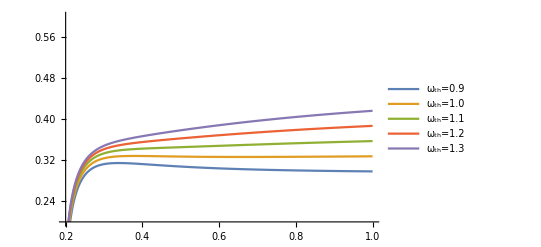

```mathematica
InputParameter={Subscript[N, C]->3,Subscript[α, S]->0.47,Subscript[C, F]->4/3,Subscript[C, A]->3,qqC->(-0.24)^3,ggC->0.012,qGC->0.8*(-0.24)^3,μ->1,Λ->0.55};
Plot[{Sqrt[Formfactor1*Exp[Λ/M]]/.Subscript[ω, th]->0.9/.InputParameter,Sqrt[Formfactor1*Exp[Λ/M]]/.Subscript[ω, th]->1.0/.InputParameter,Sqrt[Formfactor1*Exp[Λ/M]]/.Subscript[ω, th]->1.1/.InputParameter,
Sqrt[Formfactor1*Exp[Λ/M]]/.Subscript[ω, th]->1.2/.InputParameter,
Sqrt[Formfactor1*Exp[Λ/M]]/.Subscript[ω, th]->1.3/.InputParameter},{M,0.2,1},PlotRange->{0.2,0.6},PlotLegends->{"ω_th=0.9","ω_th=1.0","ω_th=1.1","ω_th=1.2","ω_th=1.3"}]
```

```mathematica
list0=Table[{M,Sqrt[Formfactor1*Exp[Λ/M]]/.Subscript[ω, th]->0.9/.InputParameter},{M,0.20,1,0.005}];
list3=Table[{M,Sqrt[Formfactor1*Exp[Λ/M]]/.Subscript[ω, th]->1.0/.InputParameter},{M,0.20,1,0.005}];
list4=Table[{M,Sqrt[Formfactor1*Exp[Λ/M]]/.Subscript[ω, th]->1.1/.InputParameter},{M,0.20,1,0.005}];
list5=Table[{M,Sqrt[Formfactor1*Exp[Λ/M]]/.Subscript[ω, th]->1.2/.InputParameter},{M,0.20,1,0.005}];
list6=Table[{M,Sqrt[Formfactor1*Exp[Λ/M]]/.Subscript[ω, th]->1.3/.InputParameter},{M,0.20,1,0.005}];


Export["/home/muslem-rahimi/HQET_LambdaE_H/MR_Notes/Formfactor/Order1/FO1_06.txt",list0,"Table"];
Export["/home/muslem-rahimi/HQET_LambdaE_H/MR_Notes/Formfactor/Order1/FO1_07.txt",list3,"Table"];
Export["/home/muslem-rahimi/HQET_LambdaE_H/MR_Notes/Formfactor/Order1/FO1_08.txt",list4,"Table"];
Export["/home/muslem-rahimi/HQET_LambdaE_H/MR_Notes/Formfactor/Order1/FO1_09.txt",list5,"Table"];
Export["/home/muslem-rahimi/HQET_LambdaE_H/MR_Notes/Formfactor/Order1/FO1_10.txt",list6,"Table"];
```

```mathematica
Subscript[f, B]=1/Sqrt[(mB)]*Sqrt[Formfactor1*Exp[Λ/M]]*(1+Subscript[C, F]*Subscript[α, S]/(4*Pi)*(3*Log[mb/μ]-2))/.mb->4.78/.mB->5.279/.InputParameter;
```

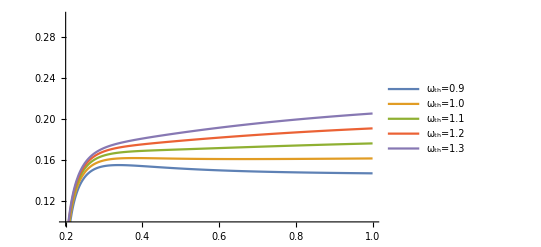

```mathematica
Plot[{Subscript[f, B]/.Subscript[ω, th]->0.9,
Subscript[f, B]/.Subscript[ω, th]->1.0,
Subscript[f, B]/.Subscript[ω, th]->1.1,Subscript[f, B]/.Subscript[ω, th]->1.2,Subscript[f, B]/.Subscript[ω, th]->1.3},{M,0.2,1},PlotRange->{0.1,0.3},PlotLegends->{"ω_th=0.9","ω_th=1.0","ω_th=1.1","ω_th=1.2","ω_th=1.3"}]
```

```mathematica
list0=Table[{M,Subscript[f, B]/.Subscript[ω, th]->0.9},{M,0.20,1,0.005}];
list1=Table[{M,Subscript[f, B]/.Subscript[ω, th]->1.0},{M,0.20,1,0.005}];
list2=Table[{M,Subscript[f, B]/.Subscript[ω, th]->1.1},{M,0.20,1,0.005}];
list3=Table[{M,Subscript[f, B]/.Subscript[ω, th]->1.2},{M,0.20,1,0.005}];
list4=Table[{M,Subscript[f, B]/.Subscript[ω, th]->1.3},{M,0.20,1,0.005}];


Export["/home/muslem-rahimi/HQET_LambdaE_H/MR_Notes/Formfactor/Order1/fBO1_06.txt",list0,"Table"];
Export["/home/muslem-rahimi/HQET_LambdaE_H/MR_Notes/Formfactor/Order1/fBO1_07.txt",list1,"Table"];
Export["/home/muslem-rahimi/HQET_LambdaE_H/MR_Notes/Formfactor/Order1/fBO1_08.txt",list2,"Table"];
Export["/home/muslem-rahimi/HQET_LambdaE_H/MR_Notes/Formfactor/Order1/fBO1_09.txt",list3,"Table"];
Export["/home/muslem-rahimi/HQET_LambdaE_H/MR_Notes/Formfactor/Order1/fBO1_10.txt",list4,"Table"];
```

##### Order O[α_S]

```mathematica
FormfactoralphaS=Subscript[N, C]*M^3/Pi^2*Integrate[z^2*Exp[-z]*(1+3*Subscript[C, F]*Subscript[α, S]/(2*Pi)*(Log[μ/(2*M*z)]+17/6+2*Pi^2/9)),{z,0,Subscript[ω, th]/M},Assumptions->{0<Subscript[ω, th]<2,0<M<1,1≤μ<5},GenerateConditions->False]-qqC*(1+3*Subscript[C, F]*Subscript[α, S]/(2*Pi))+1/(16*M^2)*qGC+Pi*Subscript[C, F]*Subscript[α, S]/(72*Subscript[N, C]*M^3)*qqC^2//Simplify
```

1/(12 π^3)M N_C ⅇ^(-ω_th/M) (C_F α_S (4 M^2 (-9 ⅇ^(ω_th/M) -ω_th/M-9 log(μ/M)+9 log(μ) ⅇ^(ω_th/M)+12 ⅇ^(ω_th/M)+2 π^2 ⅇ^(ω_th/M)+9 ℽ ⅇ^(ω_th/M)-9 log(M) ⅇ^(ω_th/M)-9 log(M/ω_th)-9 log(2) ⅇ^(ω_th/M)-2 π^2-12+log(512))-4 M ω_th (9 log(μ/M)+9 log(M/ω_th)+2 π^2+21-9 log(2))-ω_th^2 (18 log(μ/M)+18 log(M/ω_th)+4 π^2+51-18 log(2)))+12 π (2 M^2 (ⅇ^(ω_th/M)-1)-2 M ω_th-ω_th^2))+(π qqC^2 C_F α_S)/(72 M^3 N_C)-qqC ((3 C_F α_S)/(2 π)+1)+qGC/(16 M^2)

```mathematica
(*Formfactor/.Subscript[α, S]->0//Expand//Simplify*)
Subscript[f, B]=1/Sqrt[(mB)]*Sqrt[FormfactoralphaS*Exp[Λ/M]]*(1+Subscript[C, F]*Subscript[α, S]/(4*Pi)*(3*Log[mb/μ]-2))/.mb->4.78/.mB->5.279/.InputParameter;
```

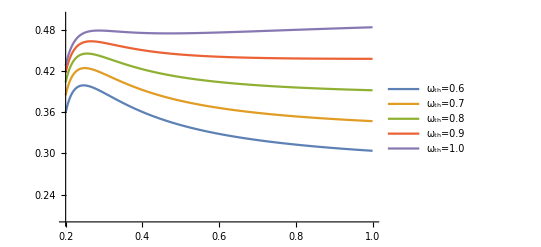

```mathematica
(*Plot*)
InputParameter={Subscript[N, C]->3,Subscript[α, S]->0.47,Subscript[C, F]->4/3,Subscript[C, A]->3,qqC->(-0.24)^3,ggC->0.012,qGC->0.8*(-0.24)^3,μ->1,Λ->0.55};
Plot[{Sqrt[FormfactoralphaS*Exp[Λ/M]]/.Subscript[ω, th]->0.6/.InputParameter,Sqrt[FormfactoralphaS*Exp[Λ/M]]/.Subscript[ω, th]->0.7/.InputParameter,Sqrt[FormfactoralphaS*Exp[Λ/M]]/.Subscript[ω, th]->0.8/.InputParameter,
Sqrt[FormfactoralphaS*Exp[Λ/M]]/.Subscript[ω, th]->0.9/.InputParameter,
Sqrt[FormfactoralphaS*Exp[Λ/M]]/.Subscript[ω, th]->1.0/.InputParameter},{M,0.2,1},PlotRange->{0.2,0.5},PlotLegends->{"ω_th=0.6","ω_th=0.7","ω_th=0.8","ω_th=0.9","ω_th=1.0"}]
```

```mathematica
list0=Table[{M,Sqrt[FormfactoralphaS*Exp[Λ/M]]/.Subscript[ω, th]->0.6/.InputParameter},{M,0.20,2,0.005}];
list3=Table[{M,Sqrt[FormfactoralphaS*Exp[Λ/M]]/.Subscript[ω, th]->0.7/.InputParameter},{M,0.20,2,0.005}];
list4=Table[{M,Sqrt[FormfactoralphaS*Exp[Λ/M]]/.Subscript[ω, th]->0.8/.InputParameter},{M,0.20,2,0.005}];
list5=Table[{M,Sqrt[FormfactoralphaS*Exp[Λ/M]]/.Subscript[ω, th]->0.9/.InputParameter},{M,0.20,2,0.005}];
list6=Table[{M,Sqrt[FormfactoralphaS*Exp[Λ/M]]/.Subscript[ω, th]->1.0/.InputParameter},{M,0.20,2,0.005}];


Export["/home/muslem-rahimi/HQET_LambdaE_H/MR_Notes/Formfactor/FalphaS_06.txt",list0,"Table"];
Export["/home/muslem-rahimi/HQET_LambdaE_H/MR_Notes/Formfactor/FalphaS_07.txt",list3,"Table"];
Export["/home/muslem-rahimi/HQET_LambdaE_H/MR_Notes/Formfactor/FalphaS_08.txt",list4,"Table"];
Export["/home/muslem-rahimi/HQET_LambdaE_H/MR_Notes/Formfactor/FalphaS_09.txt",list5,"Table"];
Export["/home/muslem-rahimi/HQET_LambdaE_H/MR_Notes/Formfactor/FalphaS_10.txt",list6,"Table"];
```

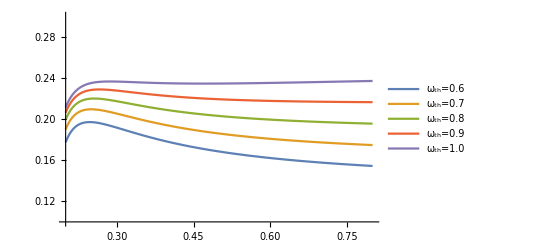

```mathematica
Plot[{Subscript[f, B]/.Subscript[ω, th]->0.6,Subscript[f, B]/.Subscript[ω, th]->0.7,Subscript[f, B]/.Subscript[ω, th]->0.8,
Subscript[f, B]/.Subscript[ω, th]->0.9,
Subscript[f, B]/.Subscript[ω, th]->1.0},{M,0.2,0.8},PlotRange->{0.1,0.3},PlotLegends->{"ω_th=0.6","ω_th=0.7","ω_th=0.8","ω_th=0.9","ω_th=1.0"}]
```

```mathematica
list0=Table[{M,Subscript[f, B]/.Subscript[ω, th]->0.6},{M,0.20,2,0.005}];
list1=Table[{M,Subscript[f, B]/.Subscript[ω, th]->0.7},{M,0.20,2,0.005}];
list2=Table[{M,Subscript[f, B]/.Subscript[ω, th]->0.8},{M,0.20,2,0.005}];
list3=Table[{M,Subscript[f, B]/.Subscript[ω, th]->0.9},{M,0.20,2,0.005}];
list4=Table[{M,Subscript[f, B]/.Subscript[ω, th]->1.0},{M,0.20,2,0.005}];


Export["/home/muslem-rahimi/HQET_LambdaE_H/MR_Notes/Formfactor/fBalphaS_06.txt",list0,"Table"];
Export["/home/muslem-rahimi/HQET_LambdaE_H/MR_Notes/Formfactor/fBalphaS_07.txt",list1,"Table"];
Export["/home/muslem-rahimi/HQET_LambdaE_H/MR_Notes/Formfactor/fBalphaS_08.txt",list2,"Table"];
Export["/home/muslem-rahimi/HQET_LambdaE_H/MR_Notes/Formfactor/fBalphaS_09.txt",list3,"Table"];
Export["/home/muslem-rahimi/HQET_LambdaE_H/MR_Notes/Formfactor/fBalphaS_10.txt",list4,"Table"];
```

##### Order [α_S] + RGE Improved

```mathematica
Subscript[γ, J0]=-3*Subscript[C, F];
Subscript[γ, J1]=Subscript[C, F]*((5/2-8/3*Pi^2)*Subscript[C, F]+(2/3*Pi^2-49/6)*Subscript[N, C]+5/3*Subscript[n, f]);
Subscript[γ, q0]=-6*Subscript[C, F];
Subscript[γ, q1]=-Subscript[C, F]*(3*Subscript[C, F]+97/3*Subscript[N, C]-10/3*Subscript[n, f]);
Subscript[γ, σ0]=Subscript[N, C]-5/Subscript[N, C];

Subscript[β, 0]=11/3*Subscript[N, C]-2/3*Subscript[n, f];
Subscript[β, 1]=34/3*Subscript[N, C]^2-10/3*Subscript[N, C]*Subscript[n, f]-2*Subscript[C, F]*Subscript[n, f];
δ=Subscript[γ, J0]/Subscript[β, 0]*(Subscript[γ, J1]/Subscript[γ, J0]-Subscript[β, 1]/Subscript[β, 0]);
alphaM=AlphasLam[0.31,2*M,4,2];
RGEFormfactor=alphaM^(-Subscript[γ, J0]/Subscript[β, 0])*(Subscript[N, C]*M^3/Pi^2*Integrate[z^2*Exp[-z]*(1+3*Subscript[C, F]*alphaM/(2*Pi)*(Log[alphaM/(2*M*z)] + 17/6+2*Pi^2/9) -alphaM*δ/(4*Pi)),{z,0,Subscript[ω, th]/M},GenerateConditions->False] -(alphaM/Subscript[α, S])^(Subscript[γ, q0]/(2*Subscript[β, 0])) *(1+(alphaM-Subscript[α, S])/(4*Pi) * (Subscript[γ, q0]/(2*Subscript[β, 0]))  *(Subscript[γ, q1]/Subscript[γ, q0]-Subscript[β, 1]/Subscript[β, 0])  +3*Subscript[C, F]*alphaM/(2*Pi)- alphaM/(4*Pi) *δ ) *qqC+1/(16*M^2)*(alphaM/Subscript[α, S])^(Subscript[γ, σ0]/(2*Subscript[β, 0]))  *qGC+Pi*Subscript[C, F]*Subscript[α, S]/(72*Subscript[N, C]*M^3)*qqC^2);
```

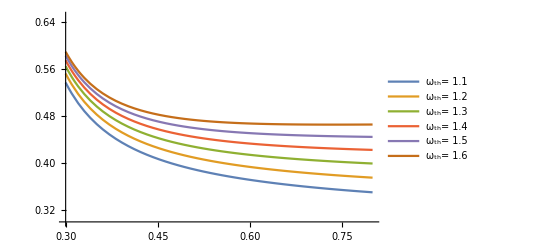

0.350399

```mathematica
InputParameter={Subscript[N, C]->3,Subscript[n, f]->4,Subscript[α, S]->0.47,Subscript[C, F]->4/3,Subscript[C, A]->3,qqC->(-0.24)^3,ggC->0.012,qGC->0.8*(-0.24)^3,Λ->0.50};
Plot[{Sqrt[RGEFormfactor*Exp[Λ/M]]/.Subscript[ω, th]->1.1/.InputParameter,Sqrt[RGEFormfactor*Exp[Λ/M]]/.Subscript[ω, th]->1.2/.InputParameter,Sqrt[RGEFormfactor*Exp[Λ/M]]/.Subscript[ω, th]->1.3/.InputParameter,Sqrt[RGEFormfactor*Exp[Λ/M]]/.Subscript[ω, th]->1.4/.InputParameter,Sqrt[RGEFormfactor*Exp[Λ/M]]/.Subscript[ω, th]->1.5/.InputParameter,Sqrt[RGEFormfactor*Exp[Λ/M]]/.Subscript[ω, th]->1.6/.InputParameter},{M,0.3,0.8},PlotLegends->{"ω_th= 1.1","ω_th= 1.2","ω_th= 1.3","ω_th= 1.4","ω_th= 1.5","ω_th= 1.6"},PlotRange->{0.3,0.65}]

Sqrt[RGEFormfactor*Exp[Λ/M]]/.Subscript[ω, th]->1.1/.InputParameter/.M->0.8
```

```mathematica
Subscript[f, B]=1/Sqrt[(mB)]*Sqrt[Formfactor*Exp[Λ/M]]*(1+Subscript[C, F]*Subscript[α, S]/(4*Pi)*(3*Log[mb/μ]-2))/.mb->4.78/.mB->5.279/.InputParameter;
```

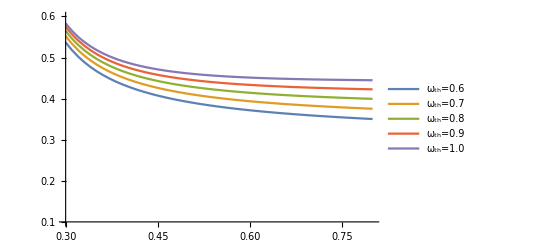

```mathematica
(*Plot*)
InputParameter={Subscript[N, C]->3,Subscript[n, f]->4,Subscript[α, S]->0.47,Subscript[C, F]->4/3,Subscript[C, A]->3,qqC->(-0.24)^3,ggC->0.012,qGC->0.8*(-0.24)^3,Λ->0.50};
Plot[{Sqrt[RGEFormfactor*Exp[Λ/M]]/.Subscript[ω, th]->1.1/.InputParameter,Sqrt[RGEFormfactor*Exp[Λ/M]]/.Subscript[ω, th]->1.2/.InputParameter,Sqrt[RGEFormfactor*Exp[Λ/M]]/.Subscript[ω, th]->1.3/.InputParameter,
Sqrt[RGEFormfactor*Exp[Λ/M]]/.Subscript[ω, th]->1.4/.InputParameter,
Sqrt[RGEFormfactor*Exp[Λ/M]]/.Subscript[ω, th]->1.5/.InputParameter},{M,0.3,0.8},PlotRange->{0.1,0.6},PlotLegends->{"ω_th=0.6","ω_th=0.7","ω_th=0.8","ω_th=0.9","ω_th=1.0"}]
```

```mathematica
(*(*Reproducing Figure 3*)
GeV=10^9;
InputParameter={Subscript[N, C]->3,Subscript[α, S]->0.47,Subscript[C, F]->4/3,qqC->(-0.24)^3*GeV^3,ggC->0.012*GeV^4,qGC->0.8*(-0.24)^3*GeV^5};

W[m_,x_]:=1-Sum[(x)^k/k! *Exp[-x],{k,0,m}]

W[2,Subscript[ω, th]/M]

LambdaH=-2*Subscript[α, S]/Pi^3*Subscript[N, C]*Subscript[C, F]*M^5*W[4,Subscript[ω, th]/M]-3*Subscript[α, S]/Pi*Subscript[C, F]*M^2*qqC*W[1,Subscript[ω, th]/M]+M/4*ggC*W[0,Subscript[ω, th]/M]-1/4*qGC;

Plot[{(LambdaH/Formfactor)*10^(-18)/.InputParameter/.Subscript[ω, th]->0.85*GeV,(LambdaH/Formfactor)*10^(-18)/.InputParameter/.Subscript[ω, th]->3*GeV,(LambdaH/Formfactor)*10^(-18)/.InputParameter/.Subscript[ω, th]->GeV},{M,0.25*GeV,GeV},PlotLegends->{0.85,1.15,1},PlotRange->{0,0.30}]*)
```

#### λ_E^2

##### Timelike region ω > 0

```mathematica
Sigma[μ_,ν_]:=I/2*(GA[μ].GA[ν]-GA[ν].GA[μ])
vTensor[μ_,ν_]:=I*(FV[v,μ].GA[ν]-FV[v,ν].GA[μ])

(*T1=1/2*I*vTensor[μ,α].Sigma[ν,α].GA5;
T2=1/2*I*vTensor[ρ,β].Sigma[σ,β].GA5;*)
T1=I*FV[v,ν].FV[v,γ].Sigma[μ,γ].GA5;
T2=I*FV[v,σ].FV[v,β].Sigma[ρ,β].GA5;


blabla[T_,μ_,ν_]:=-I/6*(Subscript[λ, H]^2*TR[T.P.GA5.Sigma[μ,ν]]+(Subscript[λ, H]^2-Subscript[λ, E]^2)*TR[T.P.GA5.vTensor[μ,ν]])//Contract/.Pair[Momentum[v],Momentum[v]] ->1//Simplify


C1=blabla[T1,μ,ν]//Contract
C2=ComplexConjugate[blabla[T2,ρ,σ]]

C1*C2/.Pair[Momentum[v],Momentum[v]] ->1
```

(v̄)^2 ((v̄)^2 (λ_ⅇ^2-λ_H^2)+λ_H^2)

(v̄)^2 ((v̄)^2 (λ_ⅇ^2-λ_H^2)+λ_H^2)

λ_ⅇ^4

```mathematica
Sigma[μ_,ν_]:=I/2*(GA[μ].GA[ν]-GA[ν].GA[μ])
vTensor[μ_,ν_]:=I*(FV[v,μ].GA[ν]-FV[v,ν].GA[μ])
P=P=(1+DiracSlash[v])/2;
blabla[T_,μ_,ν_]:=-I/6*(Subscript[λ, H]^2*TR[T.P.GA5.Sigma[μ,ν]]+(Subscript[λ, H]^2-Subscript[λ, E]^2)*TR[T.P.GA5.vTensor[μ,ν]])//Simplify
T1=I*FV[v,ν].FV[v,γ].Sigma[μ,γ].GA5;
T2=I*FV[v,σ].FV[v,β].Sigma[ρ,β].GA5;

C1=blabla[T1,μ,ν]//Contract
C2=FCChargeConjugateTransposed[blabla[T2,ρ,σ]]

C1*C2/.Pair[Momentum[v],Momentum[v]] ->1
```

(v̄)^2 ((v̄)^2 (λ_ⅇ^2-λ_H^2)+λ_H^2)

(v̄)^2 ((v̄)^2 (λ_ⅇ^2-λ_H^2)+λ_H^2)

λ_ⅇ^4

##### Spacelike region ω < 0

```mathematica
ClearAll[GeV];
(*Set GeV = 1*)
InputParameter={Subscript[N, C]->3,Subscript[n, f]->4,Subscript[α, S]->0.47,Subscript[C, F]->4/3,Subscript[C, A]->3,qqC->(-0.24)^3,ggC->0.012,qGC->0.8*(-0.24)^3,μ->1};
Subscript[Γ, 1]=I*FV[v,ν].FV[v,γ].Sigma[μ,γ].GA5;
Subscript[Γ, 2]=I*FV[v,σ].FV[v,β].Sigma[ρ,β].GA5;
P=(1+DiracSlash[v])/2;

qGCondensate3= qGC*NonAbelianContrib;


(*Der Faktor Pi/Subscript[α, S]in ggC kommt wegen der definition von Gluon Kondensat <Subscript[α, S]/Pi*G^2>*)
uptodim0 = TR[Subscript[Γ, 1].P.Subscript[Γ, 2].DiracSlash[v]].LL//Contract;

uptodim3=TR[Subscript[Γ, 1].P.Subscript[Γ, 2].DiracSlash[v]].LL+TR[Subscript[Γ, 1].P.Subscript[Γ, 2]].QQCondensate*qqC//Contract;

uptodim4=TR[Subscript[Γ, 1].P.Subscript[Γ, 2].DiracSlash[v]].LL+TR[Subscript[Γ, 1].P.Subscript[Γ, 2]].QQCondensate*qqC+TR[Subscript[Γ, 1].P.Subscript[Γ, 2].DiracSlash[v]].Coefficient[GGCondensate,DiracSlash[v]]*ggC*Pi/Subscript[α, S]//Contract;


uptodim5=TR[Subscript[Γ, 1].P.Subscript[Γ, 2].DiracSlash[v]].LL+TR[Subscript[Γ, 1].P.Subscript[Γ, 2]].QQCondensate*qqC+TR[Subscript[Γ, 1].P.Subscript[Γ, 2]].QQCondensateDim5*qGC+TR[Subscript[Γ, 1].P.Subscript[Γ, 2].DiracSlash[v]].Coefficient[GGCondensate,DiracSlash[v]]*ggC*Pi/Subscript[α, S]+TR[Subscript[Γ, 1].P.Subscript[Γ, 2].Sigma[μ,ν].(qGCondensate1)]+TR[Subscript[Γ, 1].P.Subscript[Γ, 2].qGCondensate2.Sigma[ρ,σ]]+TR[Subscript[Γ, 1].P.Subscript[Γ, 2].qGCondensate3]//Contract;


(*====================Imaginary-Part================================*)
uptodim0=uptodim0/.Pair[Momentum[v],Momentum[v]] ->1/.Log[-ω/μ]->(-HeavisideTheta[ω])//Simplify
uptodim3=uptodim3/.Pair[Momentum[v],Momentum[v]] ->1/.Log[-ω/μ]->(-HeavisideTheta[ω])//Simplify;
uptodim4=uptodim4/.Pair[Momentum[v],Momentum[v]] ->1/.Log[-ω/μ]->(-HeavisideTheta[ω])//Simplify;
uptodim5=uptodim5/.Pair[Momentum[v],Momentum[v]] ->1/.Log[-ω/μ]->(-HeavisideTheta[ω])//Simplify;
(*====================Imaginary-Part================================*)
uptodim0=Integrate[uptodim0*Exp[-ω/M],{ω,0,Subscript[ω, th]},Assumptions->{0<Subscript[ω, th]<1,0<M<1},GenerateConditions->False]//Simplify;
uptodim3=Integrate[uptodim3*Exp[-ω/M],{ω,0,Subscript[ω, th]},Assumptions->{0<Subscript[ω, th]<1,0<M<1},GenerateConditions->False]//Simplify;
uptodim4=Integrate[uptodim4*Exp[-ω/M],{ω,0,Subscript[ω, th]},Assumptions->{0<Subscript[ω, th]<1,0<M<1},GenerateConditions->False]//Simplify;
uptodim5=Integrate[uptodim5*Exp[-ω/M],{ω,0,Subscript[ω, th]},Assumptions->{0<Subscript[ω, th]<1,0<M<1},GenerateConditions->False]//Simplify
```

(ω^6 C_F N_C ω α_S)/(60 π^3)

1/(60 π^3)M ⅇ^(-ω_th/M) (C_F α_S (N_C (720 M^6 (ⅇ^(ω_th/M)-1)-720 M^5 ω_th-360 M^4 ω_th^2-120 M^3 ω_th^3-30 M^2 ω_th^4-6 M ω_th^5-ω_th^6)+30 π^2 (ω_th (qGC-12 M^2 qqC)+M (12 M^2 qqC-qGC) (ⅇ^(ω_th/M)-1)-6 M qqC ω_th^2-2 qqC ω_th^3))-15 π^3 ggC (2 M^2 (ⅇ^(ω_th/M)-1)-2 M ω_th-ω_th^2))

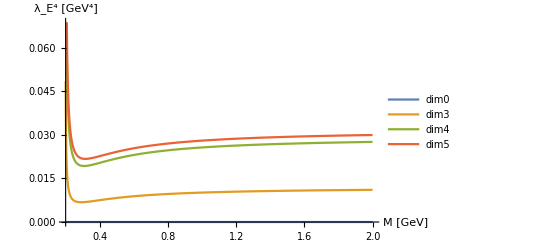

```mathematica
p1=Plot[{(uptodim0/Formfactor1)/.InputParameter/.Subscript[ω, th]->1.0,(uptodim3/Formfactor1)/.InputParameter/.Subscript[ω, th]->1.0,(uptodim4/Formfactor1)/.InputParameter/.Subscript[ω, th]->1.0,
(uptodim5/Formfactor1)/.InputParameter/.Subscript[ω, th]->1.0},{M,0.20,2},PlotLegends->{"dim0","dim3"," dim4","dim5"},AxesLabel->{"M [GeV]","λ_E^4 [GeV^4]"}]
```

```mathematica
list0=Table[{M,uptodim0/Formfactor*10/.InputParameter/.Subscript[ω, th]->1.0},{M,0.20,2,0.005}];
list3=Table[{M,uptodim3/Formfactor*10/.InputParameter/.Subscript[ω, th]->1.0},{M,0.20,2,0.005}];
list4=Table[{M,uptodim4/Formfactor*10/.InputParameter/.Subscript[ω, th]->1.0},{M,0.20,2,0.005}];
list5=Table[{M,uptodim5/Formfactor*10/.InputParameter/.Subscript[ω, th]->1.0},{M,0.20,2,0.005}];


Export["/home/muslem-rahimi/HQET_LambdaE_H/MR_Notes/Formfactor/Order1/LambdaE_dim0.txt",list0,"Table"];
Export["/home/muslem-rahimi/HQET_LambdaE_H/MR_Notes/Formfactor/Order1/LambdaE_dim3.txt",list3,"Table"];
Export["/home/muslem-rahimi/HQET_LambdaE_H/MR_Notes/Formfactor/Order1/LambdaE_dim4.txt",list4,"Table"];
Export["/home/muslem-rahimi/HQET_LambdaE_H/MR_Notes/Formfactor/Order1/LambdaE_dim5.txt",list5,"Table"];
```

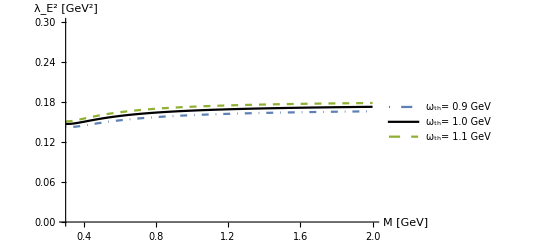

```mathematica
p2=Plot[{Sqrt[(uptodim5/Formfactor1)]/.InputParameter/.Subscript[ω, th]->0.9,
Sqrt[(uptodim5/Formfactor1)]/.InputParameter/.Subscript[ω, th]->1.0,Sqrt[(uptodim5/Formfactor1)]/.InputParameter/.Subscript[ω, th]->1.1},{M,0.3,2},PlotLegends->{"ω_th= 0.9 GeV","ω_th= 1.0 GeV"," ω_th= 1.1 GeV"},AxesLabel->{"M [GeV]","λ_E^2 [GeV^2]"},PlotRange->{0,0.3},PlotStyle->{DotDashed,Black,Dashed}]
```

```mathematica
Centralvalue=Sqrt[uptodim5/Formfactor1]/.InputParameter/.Subscript[ω, th]->0.9/.M->1.5;
error = Sqrt[uptodim5/Formfactor1]/.{Subscript[N, C]->3,Subscript[n, f]->4,Subscript[α, S]->0.47,Subscript[C, F]->4/3,Subscript[C, A]->3,qqC->(-0.24)^3,ggC->0.012,qGC->0.8*(-0.24)^3,μ->1,Subscript[ω, th]->0.9,M->1.5};
error-Centralvalue
```

0.

```mathematica
list85=Table[{M,Sqrt[uptodim5/Formfactor1]/.InputParameter/.Subscript[ω, th]->1.0},{M,0.20,2,0.005}];
list10=Table[{M,Sqrt[uptodim5/Formfactor1]/.InputParameter/.Subscript[ω, th]->1.1},{M,0.20,2,0.005}];
list115=Table[{M,Sqrt[uptodim5/Formfactor1]/.InputParameter/.Subscript[ω, th]->1.2},{M,0.20,2,0.005}];


Export["/home/muslem-rahimi/HQET_LambdaE_H/MR_Notes/Formfactor/Order1/LambdaE_0.85.txt",list85,"Table"];
Export["/home/muslem-rahimi/HQET_LambdaE_H/MR_Notes/Formfactor/Order1/LambdaE_1.0.txt",list10,"Table"];
Export["/home/muslem-rahimi/HQET_LambdaE_H/MR_Notes/Formfactor/Order1/LambdaE_1.15.txt",list115,"Table"];
```

```mathematica
Sqrt[uptodim0/Formfactor1]/.InputParameter/.Subscript[ω, th]->1.1/.M->0.8
Sqrt[uptodim3/Formfactor1]/.InputParameter/.Subscript[ω, th]->1.1/.M->0.8
Sqrt[uptodim4/Formfactor1]/.InputParameter/.Subscript[ω, th]->1.1/.M->0.8
Sqrt[uptodim5/Formfactor1]/.InputParameter/.Subscript[ω, th]->1.1/.M->0.8
```

0.0369313

0.+0.0643636 ⅈ

0.+0.109573 ⅈ

0.+0.0866497 ⅈ

```mathematica
lambdaH =0.15765350727083172
lambdaE=lambdaH-splitting
```

0.157654

0.0873911

#### λ_H^2

##### Timelike region ω >0

```mathematica
Sigma[μ_,ν_]:=I/2*(GA[μ].GA[ν]-GA[ν].GA[μ])
vTensor[μ_,ν_]:=I*(FV[v,μ].GA[ν]-FV[v,ν].GA[μ])

T1=I*(1/2*Sigma[μ,ν]-FV[v,ν].FV[v,α].Sigma[μ,α]).GA5;
T2=I*(1/2*Sigma[ρ,σ]-FV[v,σ].FV[v,β].Sigma[ρ,β]).GA5;
blabla[T_,μ_,ν_]:=-I/6*(Subscript[λ, H]^2*TR[T.P.GA5.Sigma[μ,ν]]+(Subscript[λ, H]^2-Subscript[λ, E]^2)*TR[T.P.GA5.vTensor[μ,ν]])//Contract/.Pair[Momentum[v],Momentum[v]] ->1//Simplify


C1=blabla[T1,μ,ν]//Contract
C2=ComplexConjugate[blabla[T2,ρ,σ]]

C1*C2/.Pair[Momentum[v],Momentum[v]] ->1
```

((v̄)^2-1) (v̄)^2 (λ_H^2-λ_ⅇ^2)-((v̄)^2-2) λ_H^2

((v̄)^2-1) (v̄)^2 (λ_H^2-λ_ⅇ^2)-((v̄)^2-2) λ_H^2

λ_H^4

##### Spacelike region ω <0

```mathematica
(*TR[Subscript[Γ, 1].P.Subscript[Γ, 2].DiracSlash[v]].Coefficient[GGCondensate,DiracSlash[v]]*ggC*Pi/Subscript[α, S]*)
```

```mathematica
ClearAll[GeV];
(*GeV can be set to 1*)
InputParameter={Subscript[N, C]->3,Subscript[n, f]->4,Subscript[α, S]->0.47,Subscript[C, F]->4/3,Subscript[C, A]->3,qqC->(-0.24)^3,ggC->0.012,qGC->0.8*(-0.24)^3,μ->1};
Sigma[μ_,ν_]:=I/2*(GA[μ].GA[ν]-GA[ν].GA[μ])
vTensor[μ_,ν_]:=I*(FV[v,μ].GA[ν]-FV[v,ν].GA[μ])
Subscript[Γ, 1]=I*(1/2*Sigma[μ,ν]-FV[v,ν].FV[v,α].Sigma[μ,α]).GA5;
Subscript[Γ, 2]=I*(1/2*Sigma[ρ,σ]-FV[v,σ].FV[v,β].Sigma[ρ,β]).GA5;
P=(1+DiracSlash[v])/2;


qGCondensate3= qGC*NonAbelianContrib;

(*qGCondensate1=-I*ω*Subscript[C, F]*Subscript[α, S]*Log[-ω/μ]*(GA[σ].FV[v,ρ]-GA[ρ].FV[v,σ]).DiracSlash[v];
qGCondensate2=-I*ω*Subscript[C, F]*Subscript[α, S]*Log[-ω/μ]*DiracSlash[v].(GA[σ].FV[v,ρ]-GA[ρ].FV[v,σ]);*)


(*Der Faktor Pi/Subscript[α, S]in ggC kommt wegen der definition von Gluon Kondensat <Subscript[α, S]/Pi*G^2>*)
uptodim0 = TR[Subscript[Γ, 1].P.Subscript[Γ, 2].DiracSlash[v]].LL//Contract;

uptodim3=TR[Subscript[Γ, 1].P.Subscript[Γ, 2].DiracSlash[v]].LL+TR[Subscript[Γ, 1].P.Subscript[Γ, 2]].QQCondensate*qqC//Contract;

uptodim4=TR[Subscript[Γ, 1].P.Subscript[Γ, 2].DiracSlash[v]].LL+TR[Subscript[Γ, 1].P.Subscript[Γ, 2]].QQCondensate*qqC+TR[Subscript[Γ, 1].P.Subscript[Γ, 2].DiracSlash[v]].Coefficient[GGCondensate,DiracSlash[v]]*ggC*Pi/Subscript[α, S]//Contract;


uptodim5=TR[Subscript[Γ, 1].P.Subscript[Γ, 2].DiracSlash[v]].LL+TR[Subscript[Γ, 1].P.Subscript[Γ, 2]].QQCondensate*qqC+TR[Subscript[Γ, 1].P.Subscript[Γ, 2]].QQCondensateDim5*qGC+TR[Subscript[Γ, 1].P.Subscript[Γ, 2].DiracSlash[v]].Coefficient[GGCondensate,DiracSlash[v]]*ggC*Pi/Subscript[α, S]+TR[Subscript[Γ, 1].P.Subscript[Γ, 2].Sigma[μ,ν].qGCondensate1]+TR[Subscript[Γ, 1].P.Subscript[Γ, 2].qGCondensate2.Sigma[ρ,σ]]+TR[Subscript[Γ, 1].P.Subscript[Γ, 2].qGCondensate3]//Contract;

(*====================Imaginary-Part================================*)
uptodim0=uptodim0/.Pair[Momentum[v],Momentum[v]] ->1/.Log[-ω/μ]->(-HeavisideTheta[ω])//Simplify;
uptodim3=uptodim3/.Pair[Momentum[v],Momentum[v]] ->1/.Log[-ω/μ]->(-HeavisideTheta[ω])//Simplify;
uptodim4=uptodim4/.Pair[Momentum[v],Momentum[v]] ->1/.Log[-ω/μ]->(-HeavisideTheta[ω])//Simplify;
uptodim5=uptodim5/.Pair[Momentum[v],Momentum[v]] ->1/.Log[-ω/μ]->(-HeavisideTheta[ω])//Simplify;
(*====================Imaginary-Part================================*)
uptodim0=Integrate[uptodim0*Exp[-ω/M],{ω,0,Subscript[ω, th]},Assumptions->{0<Subscript[ω, th]<1,0<M<1},GenerateConditions->False]//Simplify;
uptodim3=Integrate[uptodim3*Exp[-ω/M],{ω,0,Subscript[ω, th]},Assumptions->{0<Subscript[ω, th]<1,0<M<1},GenerateConditions->False]//Simplify;
uptodim4=Integrate[uptodim4*Exp[-ω/M],{ω,0,Subscript[ω, th]},Assumptions->{0<Subscript[ω, th]<1,0<M<1},GenerateConditions->False]//Simplify;
uptodim5=Integrate[uptodim5*Exp[-ω/M],{ω,0,Subscript[ω, th]},GenerateConditions->False]//Simplify;
```

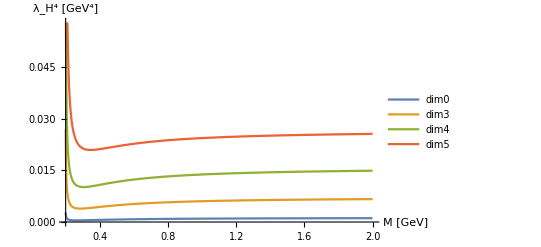

```mathematica
p1=Plot[{(uptodim0/Formfactor1)/.InputParameter/.Subscript[ω, th]->1.0,(uptodim3/Formfactor1)/.InputParameter/.Subscript[ω, th]->1.0,(uptodim4/Formfactor1)/.InputParameter/.Subscript[ω, th]->1.0,
(uptodim5/Formfactor1)/.InputParameter/.Subscript[ω, th]->1.0},{M,0.20,2},PlotLegends->{"dim0","dim3"," dim4","dim5"},AxesLabel->{"M [GeV]","λ_H^4 [GeV^4]"}]
```

```mathematica
list0=Table[{M,uptodim0/Formfactor*10/.InputParameter/.Subscript[ω, th]->1.0},{M,0.20,2,0.005}];
list3=Table[{M,uptodim3/Formfactor*10/.InputParameter/.Subscript[ω, th]->1.0},{M,0.20,2,0.005}];
list4=Table[{M,uptodim4/Formfactor*10/.InputParameter/.Subscript[ω, th]->1.0},{M,0.20,2,0.005}];
list5=Table[{M,uptodim5/Formfactor*10/.InputParameter/.Subscript[ω, th]->1.0},{M,0.20,2,0.005}];


Export["/home/muslem-rahimi/HQET_LambdaE_H/MR_Notes/Formfactor/Order1/LambdaH_dim0.txt",list0,"Table"];
Export["/home/muslem-rahimi/HQET_LambdaE_H/MR_Notes/Formfactor/Order1/LambdaH_dim3.txt",list3,"Table"];
Export["/home/muslem-rahimi/HQET_LambdaE_H/MR_Notes/Formfactor/Order1/LambdaH_dim4.txt",list4,"Table"];
Export["/home/muslem-rahimi/HQET_LambdaE_H/MR_Notes/Formfactor/Order1/LambdaH_dim5.txt",list5,"Table"];
```

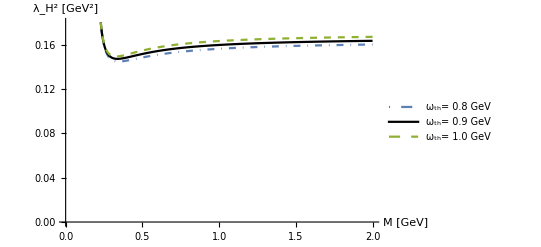

```mathematica
p2=Plot[{Sqrt[(uptodim5/Formfactor1)]/.InputParameter/.Subscript[ω, th]->1.0,
Sqrt[(uptodim5/Formfactor1)]/.InputParameter/.Subscript[ω, th]->1.1,Sqrt[(uptodim5/Formfactor1)]/.InputParameter/.Subscript[ω, th]->1.2},{M,0.2,2},PlotLegends->{"ω_th= 0.8 GeV","ω_th= 0.9 GeV"," ω_th= 1.0 GeV"},PlotRange->{0,0.18},AxesLabel->{"M [GeV]","λ_H^2 [GeV^2]"},PlotStyle->{DotDashed,Black,Dashed}]
```

```mathematica
Plot[Sqrt[uptodim0/Formfactor]/Sqrt[uptodim5/Formfactor]/.InputParameter/.Subscript[ω, th]->1.1,{M,0.2,2}]
```

```mathematica
Centralvalue=Sqrt[uptodim5/Formfactor]/.InputParameter/.Subscript[ω, th]->0.9/.M->1.5;
error = Sqrt[uptodim5/Formfactor]/.{Subscript[N, C]->3,Subscript[n, f]->4,Subscript[α, S]->0.47,Subscript[C, F]->4/3,Subscript[C, A]->3,qqC->(-0.24)^3,ggC->0.012,qGC->0.8*(-0.24)^3,μ->1,Subscript[ω, th]->0.9,M->1.5};

error-Centralvalue
```

3.64986×10^-15

```mathematica
list85=Table[{M,Sqrt[uptodim5/Formfactor]/.InputParameter/.Subscript[ω, th]->1.0},{M,0.2,2,0.005}];
list10=Table[{M,Sqrt[uptodim5/Formfactor]/.InputParameter/.Subscript[ω, th]->1.1},{M,0.2,2,0.005}];
list115=Table[{M,Sqrt[uptodim5/Formfactor]/.InputParameter/.Subscript[ω, th]->1.2},{M,0.2,2,0.005}];


Export["/home/muslem-rahimi/HQET_LambdaE_H/MR_Notes/Formfactor/Order1/LambdaH_0.85.txt",list85,"Table"];
Export["/home/muslem-rahimi/HQET_LambdaE_H/MR_Notes/Formfactor/Order1/LambdaH_1.0.txt",list10,"Table"];
Export["/home/muslem-rahimi/HQET_LambdaE_H/MR_Notes/Formfactor/Order1/LambdaH_1.15.txt",list115,"Table"];
```

```mathematica
uptodim0/Formfactor1/.InputParameter//.Subscript[ω, th]->1.1/.M->0.8
Sqrt[uptodim5/Formfactor1]/.InputParameter/.Subscript[ω, th]->1.0/.M->0.95
```

0.00136392

0.155819

```mathematica
f[x_]:=Assuming[-30<x<30,Sqrt[x^2]//Simplify]
f[-5]
```

5